Info on the notebook:
This notebook uses the BiGONLight package to compute observables in conformal Szekeres model.
It is structured as follows: 
- model set-up:  give the 4D metric tensor components as input and compute the 3+1 quantities lapse α, shift β^i, spatial metric γ_ij, extrinsic curvature K_ij and the normal vector n^μ;
- geodesic: provide initial position and tangent vector {x^μ, ℓ^μ} as input to find null geodesics;
- parallel transported frame: give the initial conditions for a frame (ϕ^μ)_αthat will be parallel transported along the computed geodesic (we use the SNF, i.e. (ϕ^μ)_α={u^μ,(ϕ^μ)_1,(ϕ^μ)_2, ℓ^μ} with u^μ the four-velocity and (ϕ^μ)_A two orthonormal vectors)
- optical tidal matrix: compute the optical tidal matrix (R^μ)_ρσν ℓ^ρ ℓ^σ in the parallel propagated frame; 
- BGO: compute and solve the Geodesic Deviation Equation for the Bi-local Geodesic Operators along the null geodesic;
- observables: compute the optical observables in the BGO framework: redshift, redshift drift, angular diameter distance, luminosity distance, parallax distance, distance slip, convergence and shear.

Set the current directory as working directory and load the package.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["bigonlight6`"]
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`70."&);
```

a generic direction can be written as 𝓋^μ=𝓋^0∂_0 +ψ(sinχ cosξ ∂_1 +sinχ sinξ ∂_1 +cosχ ∂_3)=(𝓋^0(∂_0))^μ+ψ (N⃗)^μ with respect to the local tetrad ∂_μ . 
In particular for a null direction 𝓋^0=±1 and ψ=1 , while for a timelike direction 𝓋^0=±c γ and ψ=c γ β  where β=vel/c the normalized velocity and γ=1/(√(1-β^2)) the Lorentz factor.

BGO=<<”BGO_data.m”;
totN=<<”geodesic_data.m”;

```mathematica
𝒱[Vt_,lorentz_,direction1_,direction2_]:=
Module[{V0=Vt, γ=lorentz,χ=direction1,ξ=direction2},
V0{1,0,0,0}+γ(Sin[χ]Cos[ξ]{0,1,0,0}+Sin[χ]Sin[ξ]{0,0,1,0}+Cos[χ]{0,0,0,1})
]
```

```mathematica
StandardPlotStyle[size_,sizelegend_,ylabel_,xlabel_,title_,legend_,position_]:=Module[{ft=size,ftL=sizelegend,yL=ylabel,xL=xlabel,pt=title,list=legend,pl=position},
If[ list=={},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft]},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft],PlotLegends->Placed[LineLegend[Table[Style[list[[m]],FontSize->ftL],{m,1,Length[list]}]],pl]},Print["Error"]]];
```

# Szekeres class II (conformal Meures & Bruni ArXiv:1103.0501)

In this notebook we use geometric units G=c=1. This allows us to express mass, length and  time as the same unit. For our convenience, we will express all quantities as dimension-less quantities in units of length L. Therefore, any physical quantity Q^phys=Q^comp L^α where α is a certain exponent and Q^comp is dimensionless. 
As shown in Meures & Bruni (2011), the dynamics of this model splits into a flat ΛCDM background and a non-linear dynamics for the inhomogeneities. 
Therefore, we choose to use the ΛCDM background to set-up the characteristic length L  equal to the conformal time today in Mpc η_0==L .
From Friedmann equation, η=1/ℋ_0∫(a^(-1/2)ⅆa)/((Ω_m0+Ω_Λ a^3)^(1/2)) , solving the integral and using a_0==1, we finally have L=η_0=14415.175 Mpc
The dimensionless computational present time and the dim-less hubble constant are η_0^comp==η_0/L==1  and  𝒽_0^comp==ℋ_0 L==2.246 10^-4  
Knowing the conformal time as function of the scale factor η(a), we can use the expression for the redshift in FLRW, 
									z+1=a_𝒪/a 
to find the value of a_in corresponding to a given z_in. Then the initial conformal time is found as η_in==η(a_in).
 Alternatively, one can use a specific value for a_in, like the one we used here  a_in== a_EdS==10^-4.

## Units and Parameters

```mathematica
L=(EllipticF[ArcCos[((1+(1-Sqrt[3])1(ΩΛ/Ωm0)^(1/3))/(1+(1+Sqrt[3])1(ΩΛ/Ωm0)^(1/3)))/.{Ωm0->0.3153, ΩΛ->0.6847}],(2+Sqrt[3])/4]/((H0 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3))/.{Ωm0->0.3153, ΩΛ->0.6847,H0->67.36/299792.458})) (*Mpc*)

𝒽0=(EllipticF[ArcCos[((1+(1-Sqrt[3])1(ΩΛ/Ωm0)^(1/3))/(1+(1+Sqrt[3])1(ΩΛ/Ωm0)^(1/3)))/.{Ωm0->0.3153, ΩΛ->0.6847}],(2+Sqrt[3])/4]/(( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3))/.{Ωm0->0.3153, ΩΛ->0.6847})) 
ηin=(EllipticF[ArcCos[((1+(1-Sqrt[3])0.0001(ΩΛ/Ωm0)^(1/3))/(1+(1+Sqrt[3])0.0001(ΩΛ/Ωm0)^(1/3)))/.{Ωm0->0.3153, ΩΛ->0.6847}],(2+Sqrt[3])/4]/(( 3^(1/4)𝒽0(ΩΛ)^(1/6)(Ωm0)^(1/3))/.{Ωm0->0.3153, ΩΛ->0.6847})) 
ETA0=1
START=TimeObject[Now]
```

14415.1749294347360096684854207765183902700577486166574583760745894401

3.23892798946504457297344410826874863799472597121445278785569843903373

0.010996809905676964848022975484204209101262185367397035254164872287809

1

10:02:05GMT+1.TimeObject[{10,2,5.337364},TimeZone→1.]

The free-function of the model is β_+ and it can be linked to the gravitational potential using the expression of the first order density contrast. 
The density contrast in Szekeres is δ=-(β_+𝒟)/(A+β_+𝒟)that expanded at first order is δ_1=-β_+𝒟. On the other hand, we have that the density contrast at first order in standard perturbation theory is δ_1=2/3 Δϕ_0/(ℋ_0 Ω_m0)𝒟, where ϕ_0 is the gravitational potential. From a direct comparison, follows that β_+=-2/3 Δϕ_0/(ℋ_0 Ω_m0).
In this notebook, we use a sinusoidal form for the gravitational potential, defined as:

									ϕ_0[x]=ℐ Sin[(2π)/k x]
with inhomogeneities periodic over a scale k = 500 Mpc and with intensity ℐ defined setting the value of the maximum of the  density contrast today  equal to δ_0^max==0.1.
We are still left with the function A[x,y,z]: in the following, we focus on the case of axial symmetry, in which A[x, y, z]=1+β_+B [y^2+z^2]. Therefore, in general δ_0depends on all spatial coordinates. We can consider to set ℐ along the x-axis in order to have y=z=0  (reducing A=1) and Max[Sin[(2π)/k x]]==1.
In conclusion, the intensity is determined solving:

							δ_0=(2/3(ℐ ((2π)/k)^2)/(ℋ_0^2 Ωm0)𝒟[η_0])/(A-2/3(ℐ ((2π)/k)^2)/(ℋ_0^2 Ωm0)𝒟[η_0])=0.1. 
Note that we  normalise 𝒟[η_0]=1 and that the computational value for k is k^comp=k^phys/L==500/L.

```mathematica
λ500=500/L;
P500=First[P/.Solve[Evaluate[(2/3(P ((2π)/λ500)^2)/((𝒽0^2 Ωm0)/.{Ωm0->0.3153, ΩΛ->0.6847}))]/Evaluate[(1-2/3(P((2π)/λ500)^2)/((𝒽0^2 Ωm0)/.{Ωm0->0.3153, ΩΛ->0.6847}))]==0.1,P]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.000013745659060971387969919016876011109071550642090088402133663738329027

```mathematica
param={ω->(2π)/λ500,Amp->P500,Ωm0->0.3153, ΩΛ->0.6847, c->1}(*arXiv:1807.06209 (Tab 2 5th column) , H0 units: km/s(Mpc)^-1. Regarding anl I have used "A&A 594,A17 (2016)" since the results from Plank2018 have to be published jet: Subscript[f, nl]==0.8-> Subscript[f, nl]==5/3(Subscript[a, nl]-1)-> Subscript[a, nl]==3/5 Subscript[f, nl]+1*)
```

{ω→181.146430634095731182423482097145018267504243021850751551455323863724,Amp→0.000013745659060971387969919016876011109071550642090088402133663738329027,Ωm0→0.3153,ΩΛ→0.6847,c→1}

## Model set-up

We need to provide the spacetime metric g_μν. 
This can be done in two ways: 
		1)  writing the analytic expression for the metric components g_μν=(g_00 | g_01 | g_02 | g_03
g_10 | g_11 | g_12 | g_13
g_20 | g_21 | g_22 | g_23
g_30 | g_31 | g_32 | g_33) 
		2) import data from a (relativistic) numerical simulation. 
		
In this case, we know the form of the metric g_μν, so we use the first method.

```mathematica
Clear[A,𝒟,ϕ,ℋ,𝒜,ℱ]
```

```mathematica
Clear[α,β,g,K,g4,X,V,e,Energy,nd,nu,x,y,z,η]
```

```mathematica
X4={η,x,y,z};
X={x,y,z};
V={v1,v2,v3};
e={e1,e2,e3};
Energy={energy, affine};
```

```mathematica
g4={{-(A[η])^2,0,0,0},{0,(A[η])^2(𝒜[x,y,z]+ℱ[η,x])^2,0,0},{0,0,(A[η])^2,0},{0,0,0,(A[η])^2}};
```

```mathematica
solADM=ADM[g4,X4];
α=Evaluate[solADM[[1]]]
β=Evaluate[solADM[[2]]]
g=Evaluate[solADM[[3]]]
K=Evaluate[solADM[[4]]]
nu=Evaluate[solADM[[5]]]
nd=Evaluate[solADM[[6]]]
```

√(A[η]^2)

{0,0,0}

{{A[η]^2 (𝒜[x,y,z]+ℱ[η,x])^2,0,0},{0,A[η]^2,0},{0,0,A[η]^2}}

{{-(√(A[η]^2) (𝒜[x,y,z]+ℱ[η,x]) (𝒜[x,y,z] A'[η]+ℱ[η,x] A'[η]+A[η] ℱ^(1,0)[η,x]))/A[η],0,0},{0,-(√(A[η]^2) A'[η])/A[η],0},{0,0,-(√(A[η]^2) A'[η])/A[η]}}

{1/(√(A[η]^2)),0,0,0}

{-√(A[η]^2),0,0,0}

```mathematica
αα[τ_]:=α/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ββ[τ_]:=β/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
VV[η_]:=Table[V[[i]][η],{i,1,Length[X]}];
gg[τ_]:=g/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
gg4[τ_]:=g4/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
nup[τ_]:=nu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ndown[τ_]:=nd/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];

αlup[η_]:=(*EBG[η]*)αα[η] (nup[η]+Flatten[{0,VV[η]}]);
αldown[η_]:=(*EBG[η]*)αα[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
```

## Geodesic

```mathematica
geodSz=GeodesicEquations[X,V,g,K,α,β,η]
```

{x'[η]==√(A[η]^2) v1[η],v1'[η]==√(A[η]^2) (-(2 √(A[η]^2) v1[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]]))/(A[η]^3 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]))+v1[η] ((√(A[η]^2) v2[η]^2 A'[η])/A[η]+(√(A[η]^2) v3[η]^2 A'[η])/A[η]+1/A[η]√(A[η]^2) v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]]))-(2 v1[η] v3[η] 𝒜^(0,0,1)[x[η],y[η],z[η]])/(𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]])-(2 v1[η] v2[η] 𝒜^(0,1,0)[x[η],y[η],z[η]])/(𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]])-(v1[η]^2 (ℱ^(0,1)[η,x[η]]+𝒜^(1,0,0)[x[η],y[η],z[η]]))/(𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]])),y'[η]==√(A[η]^2) v2[η],v2'[η]==√(A[η]^2) (-(2 √(A[η]^2) v2[η] A'[η])/A[η]^3+v2[η] ((√(A[η]^2) v2[η]^2 A'[η])/A[η]+(√(A[η]^2) v3[η]^2 A'[η])/A[η]+1/A[η]√(A[η]^2) v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]]))+v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,0)[x[η],y[η],z[η]]),z'[η]==√(A[η]^2) v3[η],v3'[η]==√(A[η]^2) (-(2 √(A[η]^2) v3[η] A'[η])/A[η]^3+v3[η] ((√(A[η]^2) v2[η]^2 A'[η])/A[η]+(√(A[η]^2) v3[η]^2 A'[η])/A[η]+1/A[η]√(A[η]^2) v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]]))+v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,0,1)[x[η],y[η],z[η]])}

```mathematica
enereqSz=EnergyEquations[g,K,α,β,Energy,X,V,η]
```

{energy'[η]==√(A[η]^2) energy[η] (-(√(A[η]^2) v2[η]^2 A'[η])/A[η]-(√(A[η]^2) v3[η]^2 A'[η])/A[η]-1/A[η]√(A[η]^2) v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])),affine'[η]==(√(A[η]^2))/energy[η]}

Specify the functions used in the metric

```mathematica
Clear[A,𝒟,ϕ,ℋ]
```

```mathematica
A[η_]=((Ωm0/ΩΛ)^(1/3)((1-JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])/(-1+√3+(1+√3) JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])))/.param(*from 1109.2258*);
normalizzazione=5/2 Ωm0-((5/2 Ωm0)-(A[η]Sqrt[1+ΩΛ/Ωm0 A[η]^3]Hypergeometric2F1[3/2,5/6,11/6,-ΩΛ/Ωm0 A[η]^3])/.η->ETA0)/.param;
𝒟[η_]=(A[η]/(normalizzazione)Sqrt[1+ΩΛ/Ωm0 A[η]^3]Hypergeometric2F1[3/2,5/6,11/6,-ΩΛ/Ωm0 A[η]^3])/.param;
ϕ[x_]=(Amp Sin[ω  x])/.param;
βp[x_]:=-(2  ϕ''[x])/(3 (𝒽0)^2 Ωm0)/.param;
ℱ[η_,x_]:= 𝒟[η] βp[x];
(*(𝒽0/L) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;*)
```

```mathematica
Clear[BN]
```

```mathematica
BN=Evaluate[((1/2(3/2(𝒽0^2 Ωm0)/A[η] ℱ[η,x]+A'[η]/A[η] D[ℱ[s,x],s]))/βp[x])/.param/.s->η]/.{x->1,η->1}
𝒜[x_,y_,z_]=1+βp[x]BN(y^2+z^2)/.param;
ℋ[η_]=(𝒽0) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;
```

5.247090045259113411537775679357509456690041798688101226384722+0. ⅈ

### Initial conditions

The initial conditions can be given in two different ways:
1) directly specifying the values or
2) giving the initial direction v^2 and v^3 and use the function InitialConditions[] to compute v^1 such that the geodesic is null.

```mathematica
κ=SetPrecision[(*A[ηin]^-2*)𝒱[-1,1,π/2,0],70]
TimeObject[Now]
```

{-1.,1.,0,0}

10:02:37GMT+1.TimeObject[{10,2,37.226658},TimeZone→1.]

```mathematica
(g4.κ.κ)/.{η->ETA0,x->0,y->0,z->0}/.param
```

0.

The vector κ^μ must be expressed in 3+1 form κ^μ=E(n^μ+V^μ) where E=-κ^μ n_μ and V^μ=κ^μ/E-n^μ

```mathematica
ϵ=SetPrecision[-∑_(i=1)^4 κ[[i]]nd[[i]]/.{η->ETA0,x->0,y->0,z->0},70]
vi=SetPrecision[Table[(κ[[i]]/ϵ-nu[[i]])/.{η->ETA0,x->0,y->0,z->0},{i,1,4}],70]
```

-1.

{0,-0.9999999999999999999999999999999999999999999999999999999999999999999998,0,0}

```mathematica
substitution={η->ETA0,x->0,y->0,z->0,v2->vi[[3]],v3->vi[[4]]};
```

```mathematica
initialvel1=Flatten[InitialConditions[g,substitution,V,param]]
initialN=(*{x[ETA0]==0,y[ETA0]==0,v2[ETA0]==0,z[ETA0]==0,v3[ETA0]==0,v1[1]==-1}*)Flatten[Join[Table[(substitution[[i,1]][η]/.substitution[[1]])==substitution[[i,2]],{i,2,Length[substitution]}],{(V[[1]][η]/.substitution[[1]])==initialvel1[[2,2]](*-2.5 10^-4*)(*(V[[1]]/.initialvel1[[2]])*)}]]
E0N=ϵ(*α/.η->ηin*)(*ϵ*)
initialenergyN={Energy[[1]][ETA0]==ϵ,Energy[[2]][ETA0]==1}
```

{v1→-1.,v1→1.}

{x[1]==0,y[1]==0,z[1]==0,v2[1]==0,v3[1]==0,v1[1]==1.}

-1.

{energy[1]==-1.,affine[1]==1}

```mathematica
g.V.V/.Join[{initialvel1[[2]]},substitution]/.param
(E0N^2 g4.(nu+Join[{0},V]).(nu+Join[{0},V]))/.Join[{initialvel1[[2]]},substitution]/.param
```

1.

0.

### Solve the equations numerically, given the functions in the metric explicitly

```mathematica
AbsoluteTiming[geodesicN=Flatten[SolveGeodesic[geodSz,initialN,X,V,param,η,ηin,ETA0,"A",50,50,20,5]]]
```

{542.595,{x→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],y→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],z→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],v1→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],v2→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],v3→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
AbsoluteTiming[enerN=Flatten[SolveEnergy[enereqSz,initialenergyN,Energy,geodesicN,param,η,ηin,ETA0,"SS",50,50,20,10]]]
```

{5350.82,{energy→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],affine→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>]}}

Test that the constraint conditions are satisfied for all the evolution

Note: 	the solution can be saved in a file as: geodesic >> “file_name.m”.
		Similarly, “.m” files can be imported using the syntax:  geodesic =<<”file_name.m”

```mathematica
geodesic=Join[geodesicN,enerN];
```

```mathematica
Join[geodesicN,enerN]>>"Sz_geodesic_norm.m";
```

```mathematica
geodesic=<<"Sz_geodesic_norm.m";
```

10:07:23GMT+1.TimeObject[{10,7,23.391425},TimeZone→1.]

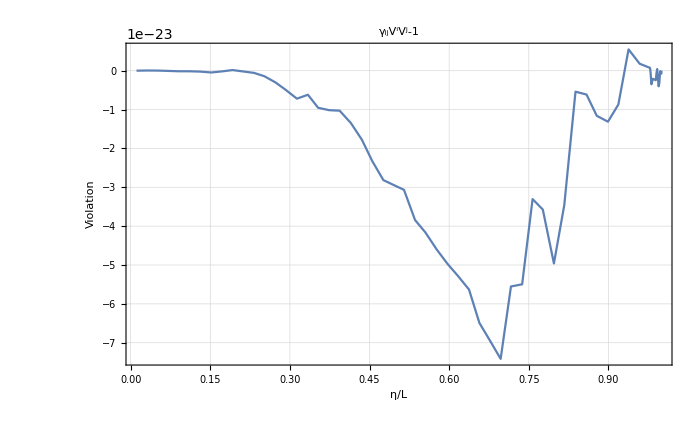

-Graphics-

```mathematica
TimeObject[Now]
EN[η_]:=energy[η]/.geodesic;
lupN[η_]:=EN[η](nup[η]+Flatten[{0,VV[η]}]);
ldownN[η_]:=EN[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
Plot[Evaluate[{gg[η].VV[η].VV[η]-1}/.geodesic/.param], {η, ηin,ETA0},PlotRange->All,WorkingPrecision->40,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","γ_ijV^iV^j-1",{},{}]]]
Plot[Evaluate[{gg4[η].lupN[η].lupN[η],lupN[η].ldownN[η]}/.geodesic/.param], {η, ηin,ETA0},PlotRange->All,WorkingPrecision->40,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","g_μνℓ^μℓ^ν",{"up-up","up-down"},{1,0.5}]]]
```

### Compute the redshift

The  redshift is defined as z+1==(g_μν u^μ ℓ^ν|_𝒮)/(g_μν u^μ ℓ^ν|_𝒪). 
In 3+1, decomposing u^μ==Γ(n^μ+U^μ) and ℓ^μ=ℰ(n^μ+V^μ), the redshift becomes: z+1==ℰ_𝒮/ℰ_𝒪(1-γ_ij V^i U^j|_𝒮)/(1-γ_ij V^i U^j|_𝒪)((1-γ_ij U^i U^j|_𝒮)/(1-γ_ij U^i U^j|_𝒪))^(1/2). In synchronous-comoving coordinates U^i==0 and the redshift simplifies to z+1==ℰ_𝒮/ℰ_𝒪

```mathematica
ZN[η_]:=EN[η]/EN[ETA0]-1
```

Compare with the analytic results:

We consider a geodesic with direction parallel to the x-axis, whose tangent vector is ℓ^μ=ℰ(1,1/(𝒜+ℱ),0,0).
We need to solve the geodesic equation for the zero-th component to obtain ℰ!

```mathematica
ℱp[η_,x_]=D[ℱ[s,x],s]/.s->η;
Eszsol=NDSolve[{es'[η]/es[η]==-2 A'[η]/A[η]-(ℱp[η,(x[η])]/(𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]))//.xSzsol,es[ETA0]==SetPrecision[lupN[ETA0][[1]]/.geodesic ,60]}/.param,es,{η,ηin,ETA0},WorkingPrecision->70,PrecisionGoal->70,InterpolationOrder->20,Method->"StiffnessSwitching",MaxSteps->10^10]
```

NDSolve::precw: The precision of the differential equation ({{es'[η]/es[η]==-(2.589934503286391808033929677056167994406610890856246538888506467250606 («1») («116» «3» JacobiSN[«2»]+«1»))/(1+Times[«2»])-(«1»)/(1+Times[«6»]+Times[«3»]),es[1]==-0.999999999999999999999999999999999999999999999999999999999559},{},{},{},{}}) is less than WorkingPrecision (70.).

{{es→InterpolatingFunction[{{0.01099680990567696484802297548420420910126218536739703525416487228780945, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
ESz[s_]=SetPrecision[First[es[s]/.Eszsol],60];
```

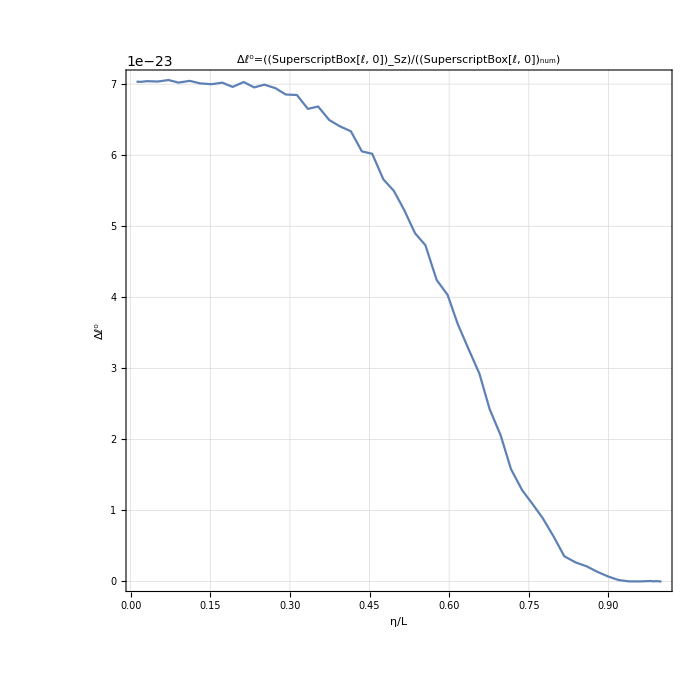

```mathematica
Plot[ESz[η]/(lupN[η][[1]])-1,{η,ηin,ETA0},PlotRange->All,AspectRatio->1, ImageSize->700,WorkingPrecision->60,Evaluate[StandardPlotStyle[16,24,"Δℓ^0","η/L","Δℓ^0=((SuperscriptBox[ℓ, 0])_Sz)/((SuperscriptBox[ℓ, 0])_num)",{},{}]]]
```

```mathematica
ZSz[η_]=SetPrecision[(A[η]ESz[η])/(A[ETA0]ESz[ETA0])-1,59];(*ESz is in physical. The redshift z=ℓ^0/a a0/(ℓ^0 0)-1 than transforming ℓ^0 conformal to physical OverBar[ℓ^0]=(ain/a)^2 ℓ^0-> z=a/a0 OverBar[ℓ^0]/(OverBar[ℓ^0] 0)-1*)
Zbg[η_]=A[ETA0]/A[η]-1;
```

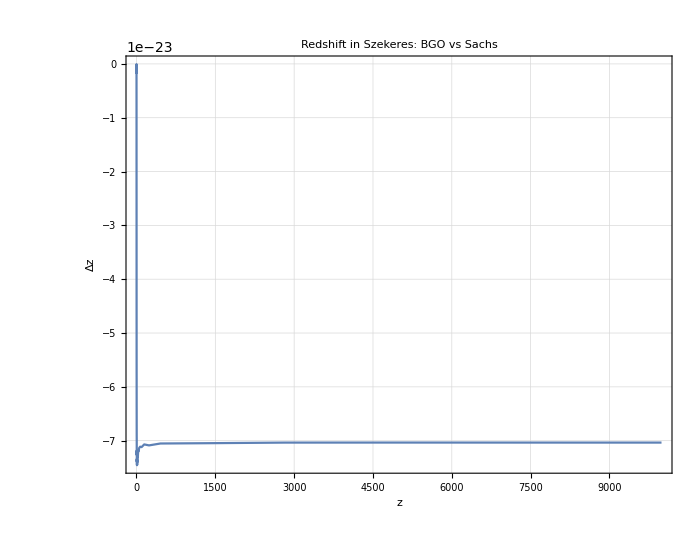

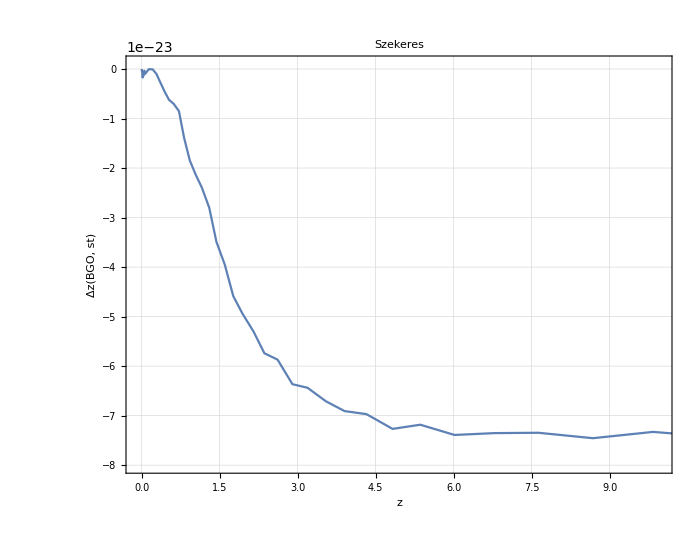

```mathematica
(*{ZNpp[η],Abs[(ZSz[η]/ZNpp[η]-1)]},*)
plotdzSz=ParametricPlot[{ZN[η],SetPrecision[(ZN[η]/ZSz[η]-1),70]},{η,ηin,ETA0},PlotRange->All,Evaluate[StandardPlotStyle[18,24,"Δz","z","Redshift in Szekeres: BGO vs Sachs",{},{}]],AspectRatio->0.8, ImageSize->700,WorkingPrecision->45]
ParametricPlot[{ZN[η],SetPrecision[(ZN[η]/ZSz[η]-1),70]},{η,ηin,ETA0},PlotRange->{{-0.1,10},{-8 10^-23,1 10^-24}},Evaluate[StandardPlotStyle[16,24,"Δz(BGO, st)","z","Szekeres",{},{}]],AspectRatio->0.8, ImageSize->700,WorkingPrecision->45]
```

Density contrast along the line of sight

```mathematica
δNpp[η_]=(-ℱ[η,x[η]]/(𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]))/.geodesic;
δNpp[ETA0]
EN[ETA0]
```

0.+0. ⅈ

-1.

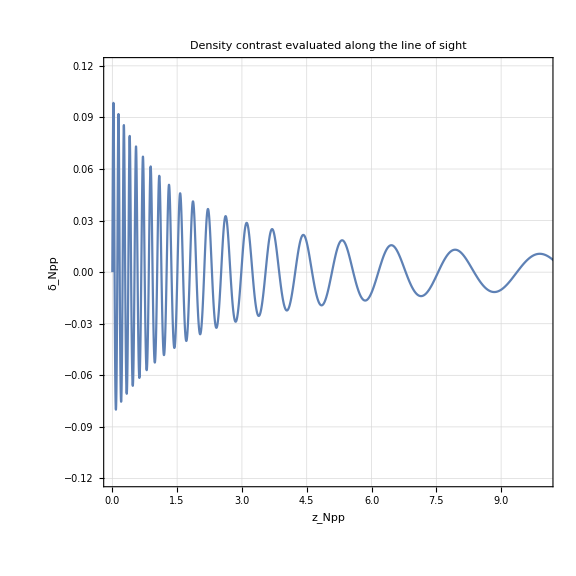

```mathematica
ParametricPlot[{ZN[η],δNpp[η]},{η,ηin,ETA0},PlotRange->{{0,10},{-0.12,0.12}},Evaluate[StandardPlotStyle[16,24,"δ_Npp","z_Npp","Density contrast evaluated along the line of sight",{},{}]],AspectRatio->1, ImageSize->Large](*AxesLabel->{Style["z_Npp",Large],Style["δ_Npp",Large]}*)
```

```mathematica
ParametricPlot[{{Zbg[η],ZNpp[η]},{Zbg[η],Zbg[η]}},{η,ηin,ETA0},PlotRange->{{0,1.2},{0,1.2}},PlotStyle->{Red,{Dotted,Blue}},Evaluate[StandardPlotStyle[16,24,"z","z_FLRW","Comparison of z_Sz and z_ΛCDM",{"z_Sz","z_ΛCDM"},{1,0.5}]],AspectRatio->0.8, ImageSize->Large]

ParametricPlot[{{Zbg[η],ZNpp[η]},{Zbg[η],Zbg[η]}},{η,ηin,ETA0},PlotRange->{{0,0.1},{0,0.1}},PlotStyle->{Red,{Dotted,Blue}},Evaluate[StandardPlotStyle[16,24,"z","z_FLRW","Close-up of comparison of z_Sz and z_ΛCDM",{"z_Sz","z_ΛCDM"},{1,0.5}]],AspectRatio->1, ImageSize->Large]
```

-Graphics-

-Graphics-

```mathematica
TimeObject[Now]
```

#### Comparison analytic geodesic

```mathematica
TimeObject[Now]
```

```mathematica
xSzsol=NDSolve[{Evaluate[x'[s]==(1/(ℱ[s,x[s]]+𝒜[x[s],y[s],z[s]]))]//.param,y'[s]==0,z'[s]==0,x[ETA0]==0,y[ETA0]==0,z[ETA0]==0},{x,y,z},{s,ηin,ETA0},WorkingPrecision->70,PrecisionGoal->70,Method->"StiffnessSwitching", InterpolationOrder->20,MaxSteps->10^10]
```

NDSolve::precw: The precision of the differential equation ({{x'[s]==1/(1+«1»«1»(0.4770081859326466737761614253961372233354583453352819296713384+0. ⅈ) Sin[«1»] (Power[«2»]+Power[«2»])),y'[s]==0,z'[s]==0,x[1]==0,y[1]==0,z[1]==0},{},{},{},{}}) is less than WorkingPrecision (70.).

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

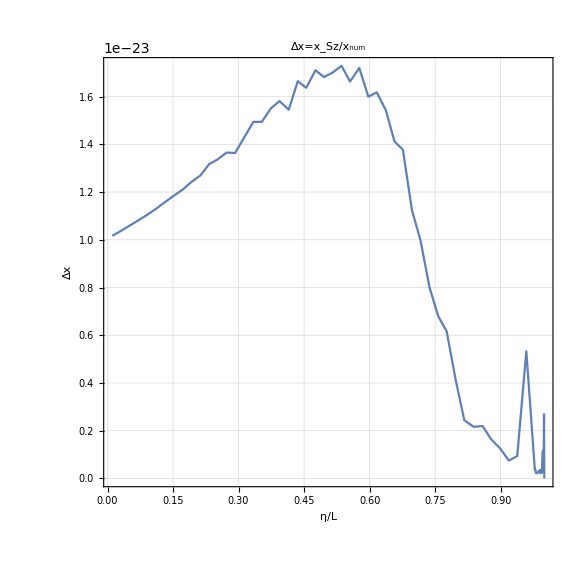

```mathematica
Plot[Abs[(x[η]/.geodesic)/(x[η]/.xSzsol)-1],{η,ηin,ETA0},PlotRange->All,ImageSize->Large, Evaluate[StandardPlotStyle[16,24,"Δx","η/L","Δx=x_Sz/x_num",{},{}]],AspectRatio->1, ImageSize->Large,WorkingPrecision->60]
```

Compute the null geodesic

```mathematica
trajectoryN[η_]:=Flatten[{x[η] ,y[η] ,z[η] }/.geodesic/.param];
Show[ParametricPlot3D[trajectoryN[η],{η,ηin,ETA0},PlotRange->{{-2,2},{- 2,2},{-2,2}}, ImageSize->700, ViewPoint->{0,0,Infinity}, AxesLabel->{"X/L","Y/L","Z/L"}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ]
```

-Graphics3D-

## Parallel transport of a frame

```mathematica
Clear[transport2,vecbcframe,soltrans2,soldeviation,solGDE,tot1,tot2,totl,totu,Cu,Cl,Cf1,Cf2,Pu,Pl,P1,P2,F,F0,EE,EE0,OPT,ξ,ξA,ξbc,Ξ,ξ4,DA,DAbc,DAsolGDE,JMAP,frame,frame0]
```

```mathematica
frame0={fu0,f10,f20,fl0};
frame={{fu1,fu2,fu3},{f11,f12,f13},{f21,f22,f23},{fl1,fl2,fl3}};
TimeObject[Now]
```

10:52:22GMT+1.TimeObject[{10,52,22.554781},TimeZone→1.]

### set-up the initial conditions for the SNF

```mathematica
(*Γl=1;
Β=0;
u[τ_]:=SetPrecision[(Γl/Sqrt[-g4[[1,1]]]{1,0,0,0}+Γl Β(Cos[0]Sin[π/2] 1/Sqrt[g4[[2,2]]]{0,1,0,0}+Sin[0]Sin[π/2] 1/Sqrt[g4[[3,3]]]{0,0,1,0}+Cos[π/2] 1/Sqrt[g4[[4,4]]]{0,0,0,1})),100]/.η->τ;*)
u[η_]:=SetPrecision[{1/A[η],0,0,0},50]
u[ETA0]//N
u[ηin]//N
```

{1.,0.,0.,0.}

{10000.,0.,0.,0.}

```mathematica
gg4[ETA0].u[ETA0].lupN[ETA0]/.Join[geodesic,param]
gg4[ETA0].u[ETA0].u[ETA0]/.η->ηin
```

1.

-1.

Assuming f_1^μ=OverTilde[f_1]^μ+A u^μ+B k^μ and f_2^μ=OverTilde[f_2]^μ+C u^μ+D k^μ+E f_1^μ, the relations between the vector of the SNF can used to determine the constants A, B, C, D and E.

```mathematica
p1={0,0,1,0};
p2={0,0,0,1};
```

```mathematica
𝒻1=Re[(p1-(gg4[t].p1.lupN[t])/(gg4[t].lupN[t].u[t])u[t]-1/(gg4[t].lupN[t].u[t])((gg4[t].p1.lupN[t])/(gg4[t].lupN[t].u[t])+gg4[t].p1.u[t])lupN[t])/.Join[geodesic,param]/.t->ETA0]
s1=𝒻1/Sqrt[gg4[ETA0].𝒻1.𝒻1]
```

{0,0,1,0}

{0,0,1.,0}

```mathematica
𝒻2=Re[(p2-(gg4[t].p2.lupN[t])/(gg4[t].lupN[t].u[t])u[t]-1/(gg4[t].lupN[t].u[t])((gg4[t].p2.lupN[t])/(gg4[t].lupN[t].u[t])+gg4[t].p2.u[t])lupN[t]-(gg4[t].p2.s1)s1)/.Join[geodesic,param]/.t->ETA0]
s2=𝒻2/Sqrt[gg4[ETA0].𝒻2.𝒻2]
```

{0,0,0,1}

{0,0,0,1.}

Initial conditions for the SN frame

```mathematica
(*u={1/A[η],0,0,0}=> fu0=α u^0 , fu^i=u^i+fu0 β^i/α;
f1=s1=> f10=α s1^0, f1^i=s1^i+f10 β^i/α;
f2=s2=> f20=α s2^0, f2^i=s2^i+f20 β^i/α;
ENW[η_]:=First[Evaluate[energy[η]/.enerNW]];
k[η_]:= Evaluate[(ENW[η](nup[η]+Flatten[{0,VV[η]}]))/.Join[geodesicNW]];
k => fl0=α k^0, fl^i=k^i+fl0 β^i/α ;*)
```

```mathematica
fu0in=(*Cu=*)SetPrecision[((-ndown[t].u[t])/.geodesic/.param)/.t->ETA0,50];
fuin=(*fu^μ=*)SetPrecision[((u[t]-(-ndown[t].u[t]) nup[t])/.geodesic/.param)/.t->ETA0,50];

f10in=(*C1=*)SetPrecision[((-ndown[t].s1)/.geodesic/.param)/.t->ETA0,50];
f1in=(*Subscript[f, 1]^μ=*)SetPrecision[((s1-(-ndown[t].s1) nup[t])/.geodesic/.param)/.t->ETA0,50];

f20in=(*C2=*)SetPrecision[((-ndown[t].s2)/.geodesic/.param)/.t->ETA0,50];
f2in=(*Subscript[f, 2]^μ=*)SetPrecision[((s2-(-ndown[t].s2) nup[t])/.geodesic/.param)/.t->ETA0,50];

fl0in=(*Ck=*)SetPrecision[((-ndown[t].lupN[t])/.geodesic/.param)/.t->ETA0,50];(*SetPrecision[A[ηin],∞];*)
flin=(*fk^μ=*)SetPrecision[((lupN[t]-(fl0in) nup[t])/.geodesic/.param)/.t->ETA0,50];
```

### Parallel transport the SNF

```mathematica
initialframeN={{fu0[ETA0]==fu0in,fu1[ETA0]==fuin[[2]],fu2[ETA0]==fuin[[3]] ,fu3[ETA0]==fuin[[4]]},{f10[ETA0]==f10in,f11[ETA0]==f1in[[2]],f12[ETA0]==f1in[[3]],f13[ETA0]==f1in[[4]]},{f20[ETA0]==f20in,f21[ETA0]==f2in[[2]],f22[ETA0]==f2in[[3]],f23[ETA0]==f2in[[4]] },{fl0[ETA0]==fl0in,fl1[ETA0]==flin[[2]],fl2[ETA0]==flin[[3]],fl3[ETA0]==flin[[4]]}};
```

```mathematica
Timing[soltransN=Flatten[PTransportedFrame[g,K,α,β,geodesicN,initialframeN,frame,frame0,param,η,ηin,ETA0,"SS",50,50,15,5]]]
```

{14210.,{fu1→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],fu2→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],fu3→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],fu0→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],f11→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],f12→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],f13→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],f10→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],f21→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],f22→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],f23→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],f20→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],fl1→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],fl2→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],fl3→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>],fl0→InterpolatingFunction[{{0.010996809905676964848022975484204209101262185367397, 1.0000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
totN=Flatten[Join[Flatten[soltransN],geodesic]];
```

```mathematica
totN=<<"Sz_ptSNF_normal.m";
```

```mathematica
Cu[η_]:=fu0[η];
Cf1[η_]:=f10[η];
Cf2[η_]:=f20[η];
Cl[η_]:=fl0[η];
Pu[η_]:={fu1[η],fu2[η],fu3[η]};
P1[η_]:={f11[η],f12[η],f13[η]};
P2[η_]:={f21[η],f22[η],f23[η]};
Pl[η_]:={fl1[η],fl2[η],fl3[η]};
```

```mathematica
Show[ParametricPlot3D[trajectoryN[η],{η,ηin,ETA0},PlotRange->{{-2,2},{-2,2},{-2,2}}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ,Graphics3D[{{Red,Arrowheads[0.02],Table[Arrow[{trajectoryN[η],(trajectoryN[η]+(Pu[η]/.totN))}],{η,ηin,ETA0,0.05}]},{Green,Arrowheads[0.02],Table[Arrow[{trajectoryN[η],(trajectoryN[η]+(P1[η]/.totN))}],{η,ηin,ETA0,0.05}]},{Blue,Arrowheads[0.02],Table[Arrow[{trajectoryN[η],(trajectoryN[η]+(P2[η]/.totN))}],{η,ηin,ETA0,0.05}]},{Black,Arrowheads[0.02],Table[Arrow[{trajectoryN[η],(trajectoryN[η]+(Pl[η]/.totN))}],{η,ηin,ETA0,0.05}]}}],Graphics3D[Sphere[{0,0,0},0.05]] , ImageSize->700,ViewPoint->{0,100,10},AxesLabel->{x,y,z},AxesStyle->Directive[Red,12]]
TimeObject[Now]
```

-Graphics3D-

16:02:39GMT+1.TimeObject[{16,2,39.076452},TimeZone→1.]

### Define the induced metric of the SNF “h”

```mathematica
Clear[F,F0,EE,EE0,Q,h]
```

```mathematica
(*((((gg4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))))/.totBG/.param)*)Q=Re[((gg4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))/.totN/.param)]
h={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
Ih=Inverse[h];
```

1.

```mathematica
F[t_]:={{Pu[t][[1]],P1[t][[1]],P2[t][[1]],Pl[t][[1]]},{Pu[t][[2]],P1[t][[2]],P2[t][[2]],Pl[t][[2]]},{Pu[t][[3]],P1[t][[3]],P2[t][[3]],Pl[t][[3]]}};
F0[t_]:={Cu[t],Cf1[t],Cf2[t],Cl[t]};
TimeObject[Now]
```

10:52:49GMT+1.TimeObject[{10,52,49.536441},TimeZone→1.]

```mathematica
(*Join[geodesic]>>"Sz_alongX_geodesic.m"*)
totN>>"Sz_ptSNF_normal.m"
```

#### Check SNF

-0.57735026630287451474075727918495279118

```mathematica
(gg4[t].u[t].s1)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].u[t].s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lupN[t].s1)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lupN[t].s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].s1.s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].s1.s1)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].s2.s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lupN[t].u[t])/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].u[t].u[t])/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lupN[t].lupN[t])/.Join[exactgeodesicBG,param]/.t->ηin
```

0.

0.

0.

«2 more identical outputs»

1.

1.

-0.0001

-1.

0.

```mathematica
Check of the relations: u^μ Subscript[u, μ]=-1,f1^μ Subscript[f1, μ]=1,f2^μ Subscript[f2, μ]=1,k^μ Subscript[k, μ]=0
```

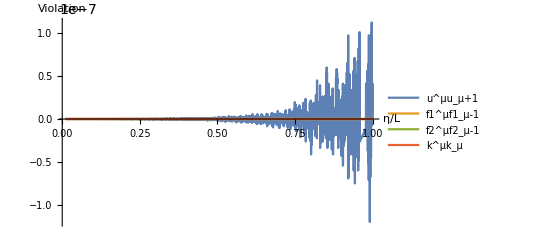

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])-1)/.totBG/.param,(gg4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])-1)/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All(*{-10^-6,10^-6}*)]
```

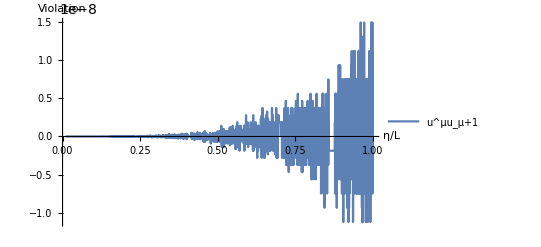

```mathematica
Plot[(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All]
```

```mathematica
Check of the relations: u^μ Subscript[f1, μ]=0,u^μ Subscript[f2, μ]=0,k^μ Subscript[f1, μ]=0,k^μ Subscript[f2, μ]=0
```

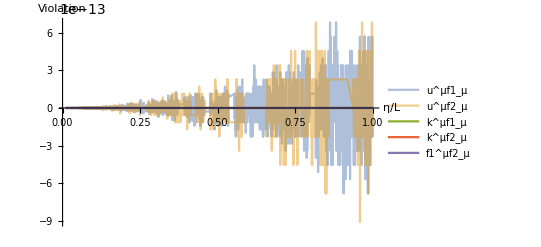

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μf1_μ","u^μf2_μ","k^μf1_μ","k^μf2_μ","f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
```

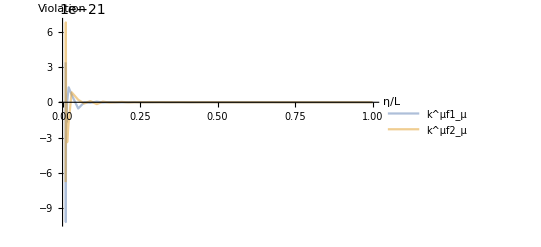

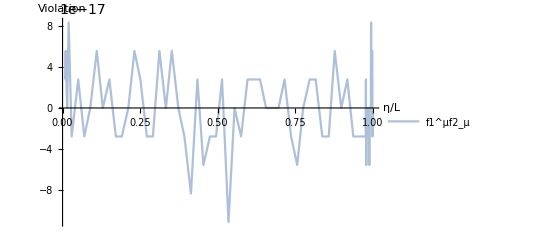

```mathematica
Plot[{(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"k^μf1_μ","k^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
Plot[{(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
```

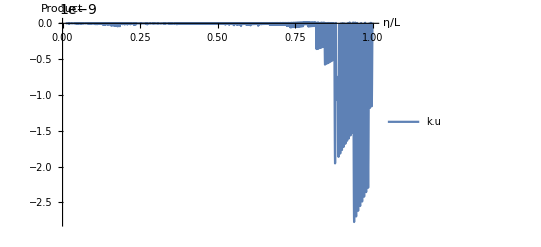

```mathematica
Plot[((((gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]])))/((gg4[ηin].(Evaluate[Cu[ηin]nup[ηin]+Flatten[{0, Pu[ηin]}]]).(Evaluate[Cl[ηin]nup[ηin]+Flatten[{0, Pl[ηin]}]]))))/.totBG/.param)-1,{η,ηin,ETA0},AxesLabel->{"η/L","Product"},PlotLegends->{"k.u"},PlotRange->All]
```

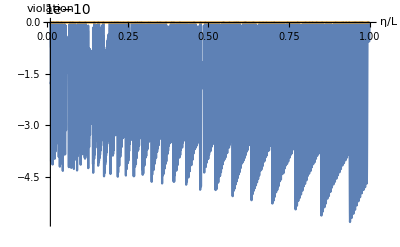

```mathematica
Plot[Evaluate[{(gg[η].VV[η].VV[η]-1),( gg[η].Pl[η].Pl[η]-Cl[η]^2) (*( (gg[η].Pl[η].Pl[η]-Cl[η]^2)/Cl[η]^2) *)}/.totBG/.param], {η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["violation",Large]}]
```

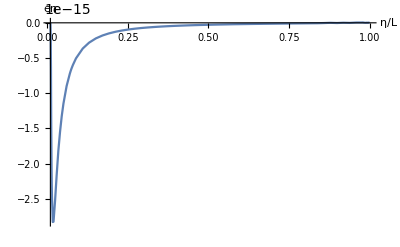

```mathematica
Plot[(A[ηin]^2/A[η]-Cl[η])/.totBG,{η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["en",Large]}]
```

## Optical Tidal Matrix

```mathematica
Clear[A,𝒟,ϕ,ℋ,ℱ,𝒜]
TimeObject[Now]
```

10:07:38GMT+1.TimeObject[{10,7,38.602027},TimeZone→1.]

```mathematica
Timing[OPT=OpticalTidalMatrix[X,V,frame,frame0,Q,g,K,α,β,η]//Simplify;]
```

{1.58259,Null}

```mathematica
OPT//N//MatrixForm
```

(0. | 0. | 0. | 0.
-1. f13[η] fu3[η] v2[η]^2 A'[η]^2+f13[η] fu2[η] v2[η] v3[η] A'[η]^2+f12[η] fu3[η] v2[η] v3[η] A'[η]^2-1. f12[η] fu2[η] v3[η]^2 A'[η]^2+((f12[η]-1. f10[η] v2[η]) (-1. fu2[η]+fu0[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η]) (-1. fu3[η]+fu0[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η]) (-1. fu1[η]+fu0[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f13[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] fu1[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f13[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f12[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f13[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f12[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η] fu1[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f12[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] fu1[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | -1. f13[η]^2 v2[η]^2 A'[η]^2+2. f12[η] f13[η] v2[η] v3[η] A'[η]^2-1. f12[η]^2 v3[η]^2 A'[η]^2-(1. ((f12[η]-1. f10[η] v2[η])^2 (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η])^2 (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η])^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]]))))/A[η]^2+2. f11[η] f13[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η]^2 v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+2. A[η]^2 f12[η] f13[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 f11[η] f13[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 f11[η] f12[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η]^2 v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. f11[η] f12[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η]^2 v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | -1. f13[η] f23[η] v2[η]^2 A'[η]^2+f13[η] f22[η] v2[η] v3[η] A'[η]^2+f12[η] f23[η] v2[η] v3[η] A'[η]^2-1. f12[η] f22[η] v3[η]^2 A'[η]^2+((f12[η]-1. f10[η] v2[η]) (-1. f22[η]+f20[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η]) (-1. f23[η]+f20[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η]) (-1. f21[η]+f20[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f13[η] f21[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] f23[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] f21[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f13[η] f22[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f12[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f13[η] f21[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] f23[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f12[η] f21[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] f22[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η] f21[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f12[η] f21[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] f22[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η] f22[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] f21[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | 0.
-1. f23[η] fu3[η] v2[η]^2 A'[η]^2+f23[η] fu2[η] v2[η] v3[η] A'[η]^2+f22[η] fu3[η] v2[η] v3[η] A'[η]^2-1. f22[η] fu2[η] v3[η]^2 A'[η]^2+((f22[η]-1. f20[η] v2[η]) (-1. fu2[η]+fu0[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f23[η]-1. f20[η] v3[η]) (-1. fu3[η]+fu0[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f21[η]-1. f20[η] v1[η]) (-1. fu1[η]+fu0[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f23[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f23[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η] fu1[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f23[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f22[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f23[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f21[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f22[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f21[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f21[η] fu1[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f22[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f22[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η] fu1[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | -1. f13[η] f23[η] v2[η]^2 A'[η]^2+f13[η] f22[η] v2[η] v3[η] A'[η]^2+f12[η] f23[η] v2[η] v3[η] A'[η]^2-1. f12[η] f22[η] v3[η]^2 A'[η]^2+((f12[η]-1. f10[η] v2[η]) (-1. f22[η]+f20[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η]) (-1. f23[η]+f20[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η]) (-1. f21[η]+f20[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f13[η] f21[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] f23[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] f21[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f13[η] f22[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f12[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f13[η] f21[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] f23[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f12[η] f21[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] f22[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η] f21[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f12[η] f21[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] f22[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η] f22[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] f21[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | -1. f23[η]^2 v2[η]^2 A'[η]^2+2. f22[η] f23[η] v2[η] v3[η] A'[η]^2-1. f22[η]^2 v3[η]^2 A'[η]^2-(1. ((f22[η]-1. f20[η] v2[η])^2 (A'[η]^2-1. A[η] A''[η])+(f23[η]-1. f20[η] v3[η])^2 (A'[η]^2-1. A[η] A''[η])+(f21[η]-1. f20[η] v1[η])^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]]))))/A[η]^2+2. f21[η] f23[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f23[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η]^2 v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+2. A[η]^2 f22[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 f21[η] f23[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 f21[η] f22[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f21[η]^2 v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. f21[η] f22[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f22[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η]^2 v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | 0.
-10000. (-1. fu3[η]^2 v2[η]^2 A'[η]^2+2. fu2[η] fu3[η] v2[η] v3[η] A'[η]^2-1. fu2[η]^2 v3[η]^2 A'[η]^2-(1. ((fu2[η]-1. fu0[η] v2[η])^2 (A'[η]^2-1. A[η] A''[η])+(fu3[η]-1. fu0[η] v3[η])^2 (A'[η]^2-1. A[η] A''[η])+(fu1[η]-1. fu0[η] v1[η])^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]]))))/A[η]^2+2. fu1[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+fu3[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+fu1[η]^2 v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+2. A[η]^2 fu2[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 fu1[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 fu1[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 fu1[η]^2 v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. fu1[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+fu2[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+fu1[η]^2 v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])) | -10000. (-1. f13[η] fu3[η] v2[η]^2 A'[η]^2+f13[η] fu2[η] v2[η] v3[η] A'[η]^2+f12[η] fu3[η] v2[η] v3[η] A'[η]^2-1. f12[η] fu2[η] v3[η]^2 A'[η]^2+((f12[η]-1. f10[η] v2[η]) (-1. fu2[η]+fu0[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η]) (-1. fu3[η]+fu0[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η]) (-1. fu1[η]+fu0[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f13[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] fu1[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f13[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f12[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f13[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f12[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η] fu1[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f12[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] fu1[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])) | -10000. (-1. f23[η] fu3[η] v2[η]^2 A'[η]^2+f23[η] fu2[η] v2[η] v3[η] A'[η]^2+f22[η] fu3[η] v2[η] v3[η] A'[η]^2-1. f22[η] fu2[η] v3[η]^2 A'[η]^2+((f22[η]-1. f20[η] v2[η]) (-1. fu2[η]+fu0[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f23[η]-1. f20[η] v3[η]) (-1. fu3[η]+fu0[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f21[η]-1. f20[η] v1[η]) (-1. fu1[η]+fu0[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f23[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f23[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η] fu1[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f23[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f22[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f23[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f21[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f22[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f21[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f21[η] fu1[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f22[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f22[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η] fu1[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])) | 0.)

The OPT’s components can have a complicated form and this cause the fail of finding a solution in NDSolve. 
There are some method which can be used to reduce the OPT’s components in a better shape and this depends case by case:
	- If the components are “good functions”, then we can use FunctionInterpolation[OPT[t][[i,j]], {t,ti,tf},InterpolationOrder→n] as components
	- alternatively, we need to discretize the function and then  interpolate. This case is very expensive and time consuming! to reduce the pain, we can use the symmetries of the Riemann tensor to reduce the number of fuctions that we need to interpolate. On top of that, we need to choose the correct step used to discretize the function.

#### Use the interpolation to make a better OPT

```mathematica
A[η_]=((Ωm0/ΩΛ)^(1/3)((1-JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])/(-1+√3+(1+√3) JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])))/.param(*from 1109.2258*);
normalizzazione=5/2 Ωm0-((5/2 Ωm0)-(A[η]Sqrt[1+ΩΛ/Ωm0 A[η]^3]Hypergeometric2F1[3/2,5/6,11/6,-ΩΛ/Ωm0 A[η]^3])/.η->ETA0)/.param;
𝒟[η_]=(A[η]/(normalizzazione)Sqrt[1+ΩΛ/Ωm0 A[η]^3]Hypergeometric2F1[3/2,5/6,11/6,-ΩΛ/Ωm0 A[η]^3])/.param;
ϕ[x_]=(Amp Sin[ω  x])/.param;
βp[x_]:=-(2  ϕ''[x])/(3 (𝒽0)^2 Ωm0)/.param;
ℱ[η_,x_]:= 𝒟[η] βp[x];
(*(𝒽0/L) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;*)
```

```mathematica
BN=Evaluate[((1/2(3/2(𝒽0^2 Ωm0)/A[η] ℱ[η,x]+A'[η]/A[η] D[ℱ[s,x],s]))/βp[x])/.param/.s->η]/.{x->1,η->1}
𝒜[x_,y_,z_]=1+βp[x]BN(y^2+z^2)/.param;
ℋ[η_]=(𝒽0) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;
```

5.247090045259113411537775679357509456690041798688101226384722+0. ⅈ

```mathematica
Simpleℛll[t_]=Evaluate[(EN[η])^2 OPT/.Join[{η->t},totN,param]];
```

```mathematica
(*step=(ETA0-ηin)/9999*)
step=(ETA0-ηin)/9999
```

0.00009891021003043534704990269272085166425629941140440073654823833660487954

step= (ETA0-ηin)/999-> 2 hour and 7 min (7634.57 sec)
step= (ETA0-ηin)/9999-> 67800.7
step=(ETA0-ηin)/99999-> ?

Note: to have a better interpolation, I have decided to multiply by a^5 the components of the (ℛ^μ)_(ℓ ℓ ν). The reason is explained in the  notebook for light propagation in the ΛCDM model. Here, I use the same trick, because the ΛCDM is the background of this Szekeres model.

```mathematica
Now
Timing[TMP=Table[{τ,A[τ]^5 Simpleℛll[τ]},{τ,ηin,ETA0,step}];]
```

Wed 3 Feb 2021 10:08:09GMT+1.

{71415.9,Null}

```mathematica
TMP=<<"SZ_res9999_TMP_normal.m";
```

```mathematica
Timing[tmp00=Table[{TMP[[i,1]],TMP[[i,2]][[1,1]]},{i,1,Length[TMP]}];
tmp01=Table[{TMP[[i,1]],TMP[[i,2]][[1,2]]},{i,1,Length[TMP]}];
tmp02=Table[{TMP[[i,1]],TMP[[i,2]][[1,3]]},{i,1,Length[TMP]}];
tmp03=Table[{TMP[[i,1]],TMP[[i,2]][[1,4]]},{i,1,Length[TMP]}];
tmp10=Table[{TMP[[i,1]],TMP[[i,2]][[2,1]]},{i,1,Length[TMP]}];
tmp11=Table[{TMP[[i,1]],TMP[[i,2]][[2,2]]},{i,1,Length[TMP]}];
tmp12=Table[{TMP[[i,1]],TMP[[i,2]][[2,3]]},{i,1,Length[TMP]}];
tmp13=Table[{TMP[[i,1]],TMP[[i,2]][[2,4]]},{i,1,Length[TMP]}];
tmp20=Table[{TMP[[i,1]],TMP[[i,2]][[3,1]]},{i,1,Length[TMP]}];
tmp21=Table[{TMP[[i,1]],TMP[[i,2]][[3,2]]},{i,1,Length[TMP]}];
tmp22=Table[{TMP[[i,1]],TMP[[i,2]][[3,3]]},{i,1,Length[TMP]}];
tmp23=Table[{TMP[[i,1]],TMP[[i,2]][[3,4]]},{i,1,Length[TMP]}];
tmp30=Table[{TMP[[i,1]],TMP[[i,2]][[4,1]]},{i,1,Length[TMP]}];
tmp31=Table[{TMP[[i,1]],TMP[[i,2]][[4,2]]},{i,1,Length[TMP]}];
tmp32=Table[{TMP[[i,1]],TMP[[i,2]][[4,3]]},{i,1,Length[TMP]}];
tmp33=Table[{TMP[[i,1]],TMP[[i,2]][[4,4]]},{i,1,Length[TMP]}];]
```

{1.06002,Null}

```mathematica
tmp[t_]=({{Interpolation[tmp00,InterpolationOrder->10][t],Interpolation[tmp01,InterpolationOrder->10][t],Interpolation[tmp02,InterpolationOrder->10][t],Interpolation[tmp03,InterpolationOrder->10][t]},{Interpolation[tmp10,InterpolationOrder->10][t],Interpolation[tmp11,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t], Interpolation[tmp13,InterpolationOrder->10][t]},{Interpolation[tmp20,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t],Interpolation[tmp22,InterpolationOrder->10][t], Interpolation[ tmp23,InterpolationOrder->10][t]},{Interpolation[tmp30,InterpolationOrder->10][t],Interpolation[tmp31,InterpolationOrder->10][t],Interpolation[tmp32,InterpolationOrder->10][t],Interpolation[tmp33,InterpolationOrder->10][t]}});
```

```mathematica
ℛab[t_]=A[t]^-5 tmp[t];
Now
```

Thu 11 Mar 2021 10:57:18GMT+1.

```mathematica
ℛll[t_]=Evaluate[((EN[η])^2 OPT/.Join[{η->t},totN,param])];
```

$Aborted

```mathematica
(Simpleℛll[t]/.t->0.9)//MatrixForm
(ℛab[t]/.t->0.9)//MatrixForm
```

(0 | 0 | 0 | 0
0 | -21.585741968481630980657993279678286069672027236+0. ⅈ | 0 | 0
0 | 0 | -21.585741968481630980657993279678286069672027236+0. ⅈ | 0
3.6421728554167793655218685308780946006671597081+0. ⅈ | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | -21.585741968481630980657905794148983299268496551+0. ⅈ | 0 | 0
0 | 0 | -21.585741968481630980657905794148983299268496551+0. ⅈ | 0
3.642172855416779365521915721612799964405056928+0. ⅈ | 0 | 0 | 0)

```mathematica
TMP>>"SZ_res9999_TMP_normal.m"
```

## 𝒲 operators

```mathematica
Mxx={{MXX00,MXX01,MXX02,MXX03},{MXX10,MXX11,MXX12,MXX13},{MXX20,MXX21,MXX22,MXX23},{MXX30,MXX31,MXX32,MXX33}};
Mxl={{MXL00,MXL01,MXL02,MXL03},{MXL10,MXL11,MXL12,MXL13},{MXL20,MXL21,MXL22,MXL23},{MXL30,MXL31,MXL32,MXL33}};
Mlx={{MLX00,MLX01,MLX02,MLX03},{MLX10,MLX11,MLX12,MLX13},{MLX20,MLX21,MLX22,MLX23},{MLX30,MLX31,MLX32,MLX33}};
Mll={{MLL00,MLL01,MLL02,MLL03},{MLL10,MLL11,MLL12,MLL13},{MLL20,MLL21,MLL22,MLL23},{MLL30,MLL31,MLL32,MLL33}};
Now
```

Thu 11 Mar 2021 10:57:24GMT+1.

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛab[η],αα[η],EN[η],param,η];
```

```mathematica
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ETA0]==0,Mll[[i,j]][ETA0]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
```

```mathematica
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totN, param,η,ηin,ETA0,"SS",50,50,20,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{175.076,Null}

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛab[η],αα[η],EN[η],param,η];
Now
```

Thu 11 Mar 2021 11:00:26GMT+1.

```mathematica
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ETA0]==KroneckerDelta[i,j],Mlx[[i,j]][ETA0]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
```

```mathematica
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totN, param,η,ηin,ETA0,"SS",50,50,20,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{341.108,Null}

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
Now
functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

Thu 11 Mar 2021 11:06:07GMT+1.

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

```mathematica
BGO=<<"SZ_res9999_BGO_normal.m";
```

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
```

```mathematica
𝒲[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

```mathematica
Now
```

Thu 11 Mar 2021 11:06:07GMT+1.

```mathematica
𝒲[ETA0]//N//MatrixForm
𝒲[ηin]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0. | 0.000420081 | 0. | 0.
0. | 0. | 0.000420081 | 0.
0.0268492 | 0. | 0. | 1.) | (0.162912 | 0. | 0. | 0.
0. | 0.0000989845 | 0. | 0.
0. | 0. | 0.0000989845 | 0.
-0.00133852 | 0. | 0. | 0.162912)
(0. | 0. | 0. | 0.
0. | -7.6013×10^6 | 0. | 0.
0. | 0. | -7.6013×10^6 | 0.
-178.791 | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | -1.78873×10^6 | 0. | 0.
0. | 0. | -1.78873×10^6 | 0.
-29.1541 | 0. | 0. | 1.))

```mathematica
Join[XXgroup,XLgroup]>>"SZ_res9999_BGO_normal.m"
```

### Forward to backwards transformation for 𝒲 operators

In the case when the initial conditions are given at the initial time, i.e. at the source, the BGO are integrated forward in time and they describe the optical properties as seen by the source: to indicate the fact that 𝒲 acts from the source 𝒮 to any point along the null geodesic p_λ, we write 𝒲(p_λ,𝒮). 
However, all observables are “seen” by the observer 𝒪, not by the source! Therefore, before of using these BGO to compute observables they need to be transformed in  𝒲(p_λ,𝒪). This can be done using the BGO properties as described in Grasso & Villa (2021) and in Grasso et. al. (2021).

The procedure to perform the transformations is encoded in this section: note that here we consider that all the quantities (meaning the geodesic and the parallel transported frame) were obtained giving the initial conditions at η_in.

Solve the GDE for BGO forward in time to obtain  𝒲(p_λ,𝒮)

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],αα[η],EBG[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ηin]==0,Mll[[i,j]][ηin]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],αα[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ηin]==KroneckerDelta[i,j],Mlx[[i,j]][ηin]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

The block matrices of 𝒲(p_λ,𝒮) are:

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
ℳ[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

Then, 𝒲(p_λ,𝒪) is obtained as:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲(𝒮,𝒪)
	where 𝒲(𝒮, 𝒪)= 𝒲^-1(𝒪,𝒮).
In other words, we need to compute the inverse of the 8x8 block matrix 𝒲^-1(𝒪,𝒮): this is not a simple task in general but, using the fact that 𝒲 is symplectic, we can find the inverse block components as:

```mathematica
WXX[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mll[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mll[[i,j]]->Mll[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLX[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mlx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mlx[[i,j]]->Mlx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WXL[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxl[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxl[[i,j]]->Mxl[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLL[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxx[[i,j]]->Mxx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
```

Then, the previous components calculated at η_0 give  𝒲^-1(𝒪,𝒮), and finally we have:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲^-1(𝒪,𝒮)

```mathematica
𝒲[η_]:=({{MXX[η].WXX[ETA0]+MXL[η].WLX[ETA0],MXX[η].WXL[ETA0]+MXL[η].WLL[ETA0]},{MLX[η].WXX[ETA0]+MLL[η].WLX[ETA0],MLX[η].WXL[ETA0]+MLL[η].WLL[ETA0]}})
```

```mathematica
𝒲[ETA0]//N//MatrixForm
ℳ[ηin]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

## Observables

### Angular diameter distance

```mathematica
Now
Timing[tmpWAB=SetPrecision[Table[𝒲[η][[1,2]][[i,j]],{i,2,3},{j,2,3}],50];]
```

Thu 11 Mar 2021 11:06:07GMT+1.

{0.018572,Null}

```mathematica
Timing[detWxlAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAB])]]]/.η->t],50];]
```

{0.154815,Null}

```mathematica
detWxlAB[ETA0]
```

0.

Here we are in synchronous-comoving gauge, meaning that all elements are comoving with respect to the cosmic expansion. In this case the observer four-velocity u^μ is equal to the normal n^μ to the foliation. In general, in other coordinates, we should take into account that the observer has a proper velocity which induce an aberration effect due to its motion: this is the described by the term g_μν ℓ^μ u^ν|_𝒪

```mathematica
(*Uvel[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG*)
Timing[
DangWxl[η_]=Evaluate[ldownN[ETA0].(nup[ETA0])Evaluate[detWxlAB[η]]/.Join[param,totN]];]
```

{0.055749,Null}

```mathematica
DangWxl[ETA0]
Now
```

0.

Thu 11 Mar 2021 11:06:08GMT+1.

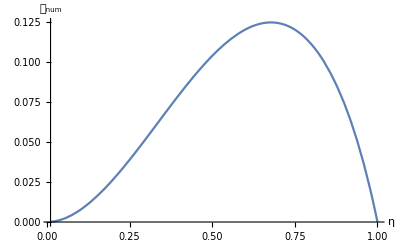

```mathematica
Plot[DangWxl[η] ,{η,ηin,ETA0},WorkingPrecision->30,AxesLabel->{"η","𝒟_num"}]
```

In ΛCDM the angular diameter distance as function of the redshift is:

```mathematica
χz[z_]:=Evaluate[1/(z+1)(1/(𝒽0 Ωm0^(1/3)ΩΛ^(1/6) 3^(1/4))(EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+((Ωm0/ΩΛ)^(1/3)(1+z)))-1],(2+Sqrt[3])/4]-EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+(Ωm0/ΩΛ)^(1/3))-1],(2+Sqrt[3])/4]))//.param];
```

#### Comarison with Szekeres

```mathematica
ℓO[s_]:=Flatten[{ESz[s],ESz[s]/(𝒜[x[s],y[s],z[s]]+ℱ[s,x[s]]),0,0}//.xSzsol](*lupN[[1]]/.geodesicN*)
```

```mathematica
dlovel[s_]:=(D[ℓO[p][[1]],p]/.p->s)/(ℓO[s][[1]])
```

```mathematica
δNpp[η_]=(-ℱ[η,x[η]]/(𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]))/.geodesic;
```

```mathematica
Timing[solDangSz=NDSolve[{da''[s]+dlovel[s]da'[s]==-3/2(𝒽0^2 Ωm0)/A[s](δNpp[s]+1)da[s],da[ETA0]==DangWxl[ETA0],da'[ETA0]==(gg4[ETA0].ℓO[ETA0].(nup[ETA0]))/(ℓO[ETA0][[1]])}//.param,da,{s,ηin,ETA0},WorkingPrecision->70,PrecisionGoal->70,Method->"StiffnessSwitching",InterpolationOrder->20, MaxSteps->10^10]]
```

NDSolve::precw: The precision of the differential equation ({{(InterpolatingFunction[{{«2»}},{5,1,20,{«1»},{«1»},{«1»},0,0,0,Automatic,{},{},False},{{«1633»}},{{«21»},{«21»},{«21»},«45»,{«21»},{«21»},«1583»},{{«2»}}][s] «1»)/(InterpolatingFunction[{«1»},{«13»},{«1»},{«1633»},{«1»}][s])+da''[s]==-(«116» da[s] («1») (1-(«1»)/(Plus[«3»] «1»)))/(1-JacobiCN[«2»]),da[1]==0.,da'[1]==-«96»},{},{},{},{}}) is less than WorkingPrecision (70.).

{7144.44,{{da→InterpolatingFunction[{{0.01099680990567696484802297548420420910126218536739703525416487228780945, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}}

```mathematica
anDangSz[t_]=First[da[η]/.solDangSz];
Precision[DangSz[ηin]]
Now
```

68.3759

Thu 11 Mar 2021 13:05:04GMT+1.

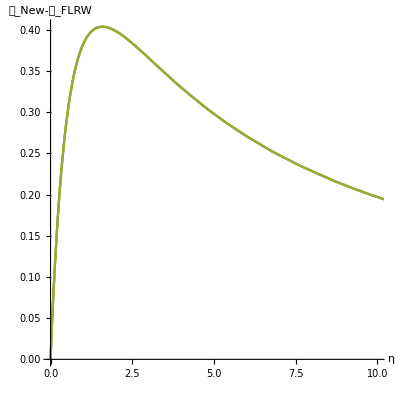

```mathematica
ParametricPlot[{{ZN[η],𝒽0 DangWxl[η] },{ZN[η],𝒽0 anDangSz[η] },{ZN[η], 𝒽0 χz[ZN[η]]}},{η,ηin,ETA0},AspectRatio->1, PlotRange->{{0,10}},WorkingPrecision->30,AxesLabel->{"η","𝒟_New-𝒟_FLRW"}]
```

```mathematica
tz10=η/.Flatten[Solve[ZN[η]==10,η]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.331371699755422296753724032622217307965250748753

-Graphics-

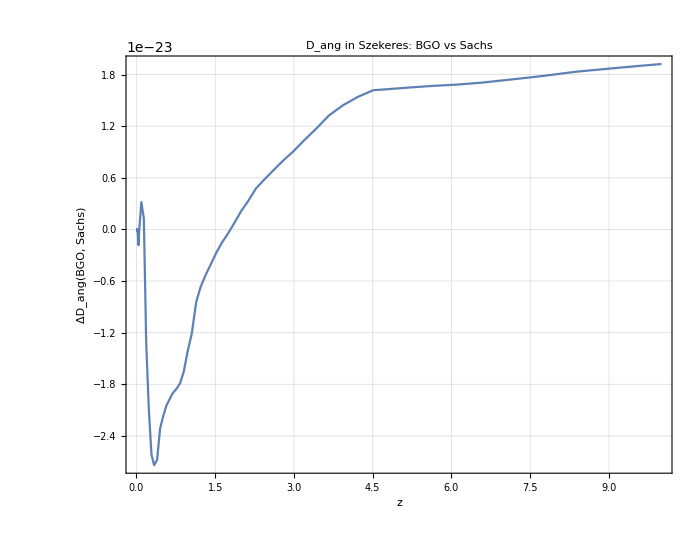

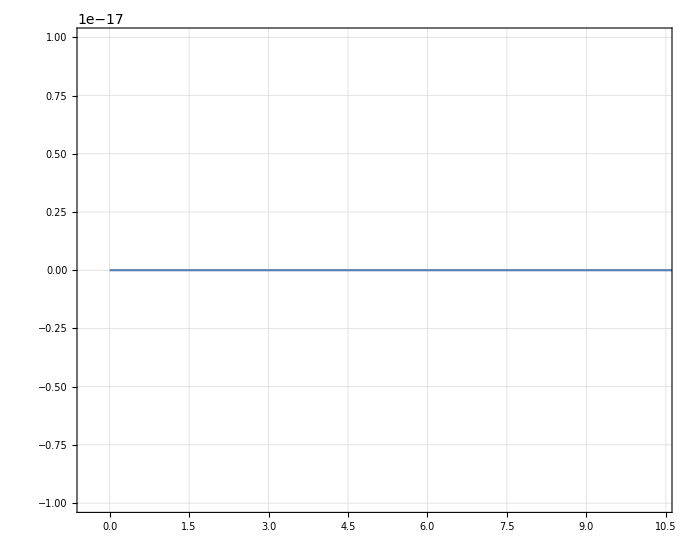

```mathematica
Graphics[{White,Rectangle[{0,0},{1,0.8}]}]
ParametricPlot[{ZN[η],(DangWxl[η]/anDangSz[η]-1)},{η,(*ηin*)tz10,ETA0},PlotRange->All,Evaluate[StandardPlotStyle[18,24,"ΔD_ang(BGO, Sachs)","z","D_ang in Szekeres: BGO vs Sachs",{},{}]],AspectRatio->0.8, ImageSize->700,WorkingPrecision->50]
ParametricPlot[{ZN[η],(DangWxl[η]/anDangSz[η]-1)},{η,ηin,ETA0},PlotRange->{{-0.4,10.4},{-1 10^-17,1 10^-17}},Evaluate[StandardPlotStyle[16,24," "," "," ",{},{}]],AspectRatio->0.8, ImageSize->700,WorkingPrecision->45]
```

### Luminosity distance and Parallax distance and the distance slip

```mathematica
(*𝒲[t_]:=𝒲2[t]*)
```

```mathematica
Timing[tmpWAA=SetPrecision[Table[𝒲[η][[1,1]][[i,j]],{i,2,3},{j,2,3}],50];]
```

{0.005216,Null}

```mathematica
Timing[detWxxAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAA])]]]/.η->t],50];]
```

{0.033076,Null}

```mathematica
Dpar[η_]=Evaluate[(gg4[ETA0].lupN[ETA0].nup[ETA0])Evaluate[detWxlAB[η]/detWxxAB[η]]/.Join[param,totN]];
```

```mathematica
DangWxl[ETA0]
Dpar[ETA0]
```

0.

0.

```mathematica
Dlum[t_]=(1+ZN[t])^2 DangWxl[t];
```

```mathematica
ParametricPlot[{{ZN[t], 𝒽0 DangWxl[t]},{redshift[t],𝒽0 Dlum[t]},{redshift[t],𝒽0 Dpar[t]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{0,1.5}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in Szekeres model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

```mathematica
ParametricPlot[{{ZN[t], 𝒽0 DangWxl[t]},{redshift[t],𝒽0 Dlum[t]},{redshift[t],𝒽0 Dpar[t]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,5},{0,15}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in Szekeres model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

```mathematica
Plot[1-DangWxl[t]^2/Dpar[t]^2 ,{t,ηin,ETA0},WorkingPrecision->30,AxesLabel->{Style["η/(M̄)",Large],Style["μ",Large]},ImageSize->Large]
ParametricPlot[{ZN[t], 1-DangWxl[t]^2/Dpar[t]^2},{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{0,1.005}},Evaluate[StandardPlotStyle[18,24,"μ","z","Distance slip in Szekeres model",{ },{ }]]]
```

### Redshift drift effects

```mathematica
𝒲XX[η_]:=Mxx/.functional[η];
𝒲LX[η_]:=Mlx/.functional[η];
𝒲XL[η_]:=Mxl/.functional[η];
𝒲LL[η_]:=Mll/.functional[η];
I𝒲XL[η_]:=Inverse[𝒲XL[η]];
```

```mathematica
Uoo[η_]:=-hDD.I𝒲XL[η].𝒲XX[η]
Uoe[η_]:=hDD.I𝒲XL[η]
Ueo[η_]:=-(hDD.𝒲LX[η]-hDD.𝒲LL[η].I𝒲XL[η].𝒲XX[η])
Uee[η_]:= -hDD.𝒲LL[η].I𝒲XL[η]
```

```mathematica
𝒰dd[η_]:= {{Uoo[η],Uoe[η]},{Ueo[η],Uee[η]}}
```

```mathematica
(*four acceleration can be calculated as a^ν==u^μ∇_μ u^ν*)
```

Note: the source and observer four-velocity and acceleration have to be projected in the parallel transported frame, since the BGO 𝒲 are expressed in the SNF.

```mathematica
e0[s_]=ldownN[s]/Q;
e1[η_]=gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])/.totN;
e2[η_]=gg4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])/.totN;
e3[η_]=(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+e0[η])/Q/.totN;
```

```mathematica
up[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
```

```mathematica
uE[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
aE[η_]:={0,0,0,0}
uO[η_]:=u[η](*{1/A[η],0,0,0}*)
aO[η_]:={0,0,0,0}
```

```mathematica
ΞDoppler[η_]:=(ldownN[η]/(uE[η].ldownN[η])).(aE[η]/(1+ZN[η]))-(ldownN[ETA0]/(uO[ETA0].ldownN[ETA0])).aO[ETA0]
lnzdrift[η_]:=(ΞDoppler[η]-1/(uO[ETA0].ldownN[ETA0])(Uoo[η].uO[ETA0].uO[ETA0]+1/(1+ZN[η])Uoe[η].uO[ETA0].uE[η]+1/(1+ZN[η])Ueo[η].uE[η].uO[ETA0]+1/(1+ZN[η])^2 Uee[η].uE[η].uE[η]))/.BGO/.geodesic
```

Dimensions: we want to give physical units to our dimensionless redshift drift. To do so, we need to convert L in the unit we want to use, i.e. in 1/s, using c and G.
							s^-1=(Mpc/s)/Mpc=[c/L]=(299792458 3.24078 10^-23)/L

```mathematica
cL=(299792458 3.24078 10^-23)/L(*c/L==(Mpc/s)/Mpc=1/s*)
```

6.73985162714454797289109821229927708517372021951910376936464821697556×10^-19

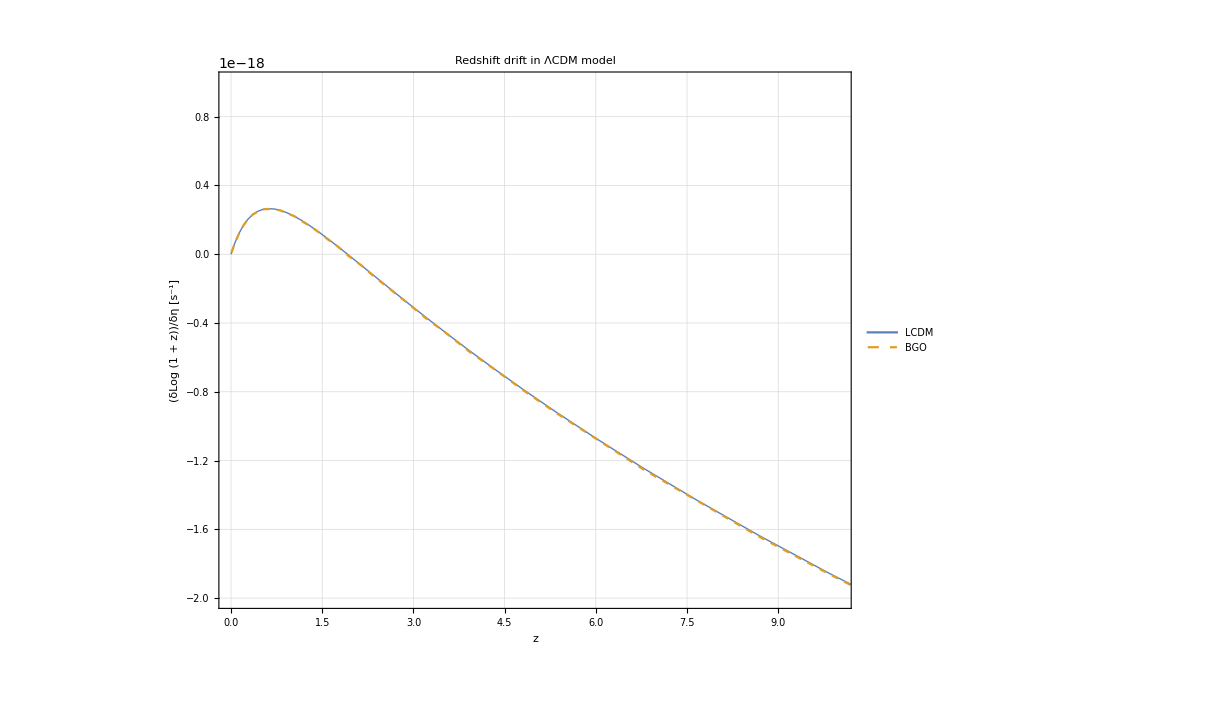

```mathematica
ParametricPlot[{{ZN[t],cL 𝒽0/(1+ZN[t])((1+ZN[t])-Sqrt[Ωm0(1+ZN[t])^3+ΩΛ])/.param},{ZN[t],cL lnzdrift[t]}},{t,ηin,ETA0},ImageSize->900,PlotRange->{{0,10},{-2 10^-18, 10^-18}},AspectRatio->0.8,PlotStyle->{Thick,Dashed},Evaluate[StandardPlotStyle[20,24,"(δLog (1 + z))/δη [s^-1]","z","Redshift drift in ΛCDM model",{"LCDM","BGO" },{0.8,0.8 }]]]
```

### Analytic Redshift drift

```mathematica
Dℱ[η_,x_]=D[ℱ[s,x],s]/.s->η;
DDℱ[η_,x_]=D[Dℱ[s,x],s]/.s->η;
```

```mathematica
pt=Precision[lnzdrift[t]]
```

48.1781

```mathematica
solδz=Flatten[NDSolve[{U'[t]==-A[ETA0]/A[t] 1/(ZSz[t]+1)((A''[t]A[t]-A'[t]^2)/A[t]^2+A'[t]/A[t] Dℱ[t,x[t]]/(𝒜[x[t],y[t],z[t]]+ℱ[t,x[t]])+DDℱ[t,x[t]]/(𝒜[x[t],y[t],z[t]]+ℱ[t,x[t]]))//.xSzsol,U[ETA0]==0},U,{t,ηin,ETA0},WorkingPrecision->70,PrecisionGoal->70,Method->"StiffnessSwitching",InterpolationOrder->20, MaxSteps->10^10]]
```

NDSolve::precw: The precision of the differential equation ({{U'[t]==-(1.29496725164319590401696483852808399720330544542812326944425323363 («1») ((«114» «1» (Times[«2»]+«1»))/Plus[«2»]^2+(«1»)/(«1»)+(«1»)/Plus[«1»]))/((1-JacobiCN[«2»]) (0.-0.77222030034434520678065145968174110304554245450183723459291 Plus[«2»] «1» InterpolatingFunction[«5»][«1»])),U[1]==0},{},{},{},{}}) is less than WorkingPrecision (70.).

{U→InterpolatingFunction[{{0.01099680990567696484802297548420420910126218536739703525416487228780945, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}

```mathematica
δz[η_]:=Evaluate[U[η]/.solδz]
tz10=t/.Flatten[Solve[ZN[t]==10,t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.331371699755422296753724032622217307965250748753

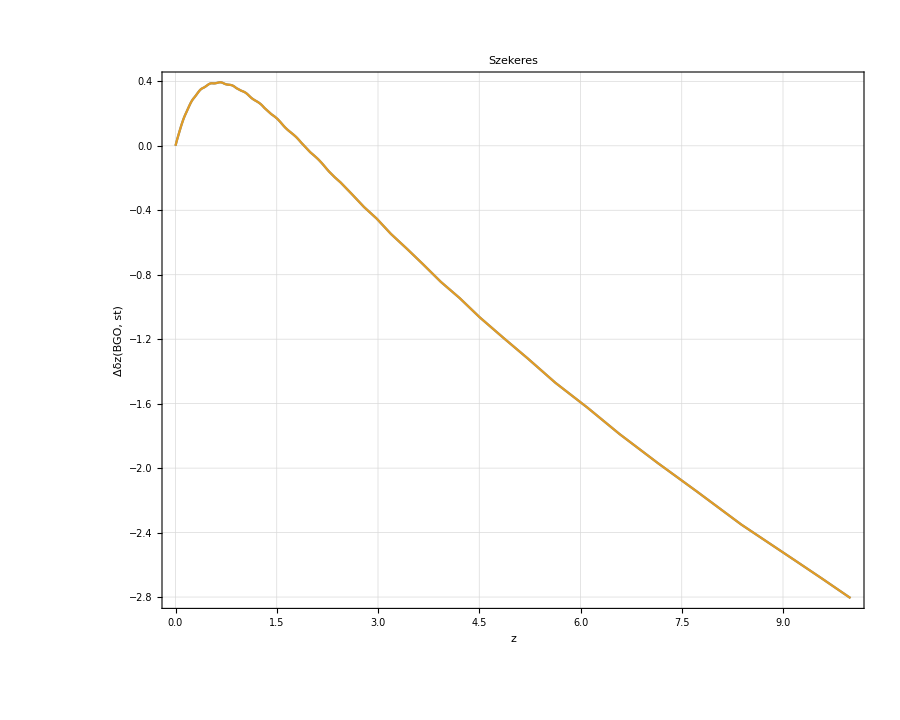

```mathematica
ParametricPlot[{{ZN[t], δz[t]},{ZN[t], lnzdrift[t]}},{t,tz10,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,(*WorkingPrecision->60,*)Evaluate[StandardPlotStyle[20,24,"Δδz(BGO, st)","z","Szekeres",{},{}]]]
```

```mathematica
Graphics[{White,Rectangle[]}]
```

-Graphics-

```mathematica
ParametricPlot[{ZN[t],(lnzdrift[t]-δz[t])/δz[t]},{t,tz10,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,WorkingPrecision->40,Evaluate[StandardPlotStyle[20,24,"Δδz(BGO, st)","z","Szekeres",{},{}]]]
```

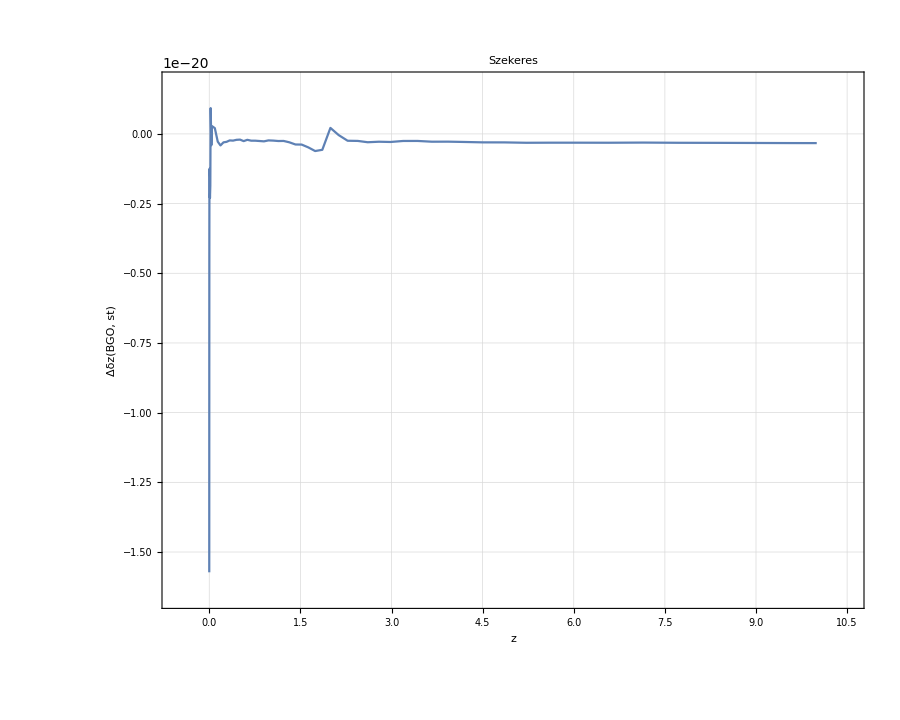

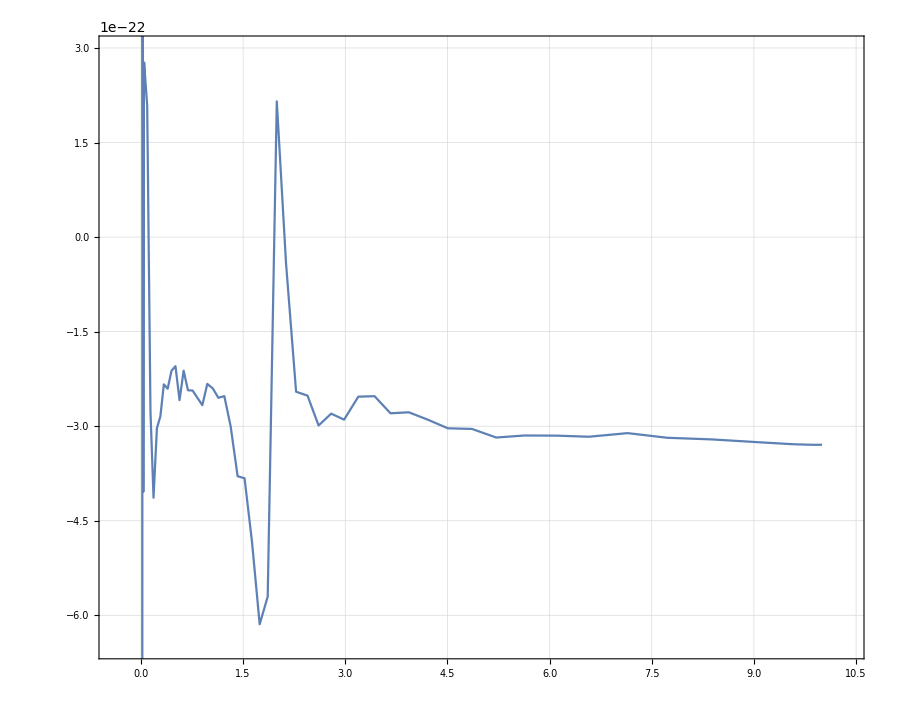

```mathematica
ParametricPlot[{ZN[t],(lnzdrift[t]-δz[t])/δz[t]},{t,tz10,ETA0},ImageSize->900,PlotRange->{{-0.4,10.4},{-6.5 10^-22,3 10^-22}},AspectRatio->0.8,WorkingPrecision->40,Evaluate[StandardPlotStyle[20,24," "," ","",{},{}]]]
```

```mathematica
{zSz->(Evaluate[ZN[#]]&),DangSz->(Evaluate[DangWxl[#]]&) ,DlumSz->(Evaluate[Dlum[#]]&) , DparLCDM->(Evaluate[Dpar[#]]&) , ZdriftLCDM->(Evaluate[lnzdrift[#]]&) }>>"observables_Szekeres_normal.m"
{ℓ0->(Evaluate[ESz[#]]&),ANzSz->(Evaluate[ZSz[#]]&),ANDangSz->(Evaluate[anDangSz[#]]&)  , ANδz->(Evaluate[δz[#]]&) }>>"AN_observables_Szekeres_normal.m"
```

### Shear and expansion

```mathematica
Timing[tmpWllAB=SetPrecision[Table[𝒲[η][[2,2]][[i,j]],{i,2,3},{j,2,3}],50];]
IWxlAB=Inverse[tmpWAB];
```

{748.61,Null}

```mathematica
trxlll[t_]=SetPrecision[Evaluate[Tr[IWxlAB.tmpWllAB]/.η->t],50];
```

```mathematica
DDang[t_]=1/2 DangWxl[t] trxlll[t];
```

```mathematica
𝒮[t_]=Evaluate[(tmpWllAB.IWxlAB)//.η->t];
```

```mathematica
expansion[η_]=Tr[𝒮[η]]/2;
shear[η_]=Sqrt[(Tr[𝒮[η].𝒮[η]]/2-(Tr[𝒮[η]]/2)^2)];
```

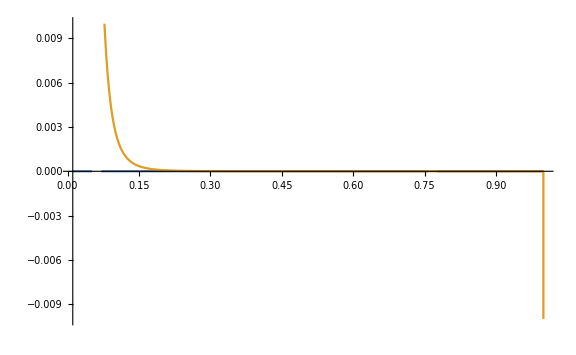

```mathematica
Plot[{shear[η],expansion[η]},{η,ηin,ETA0},ImageSize->Large,PlotRange->0.01]
```

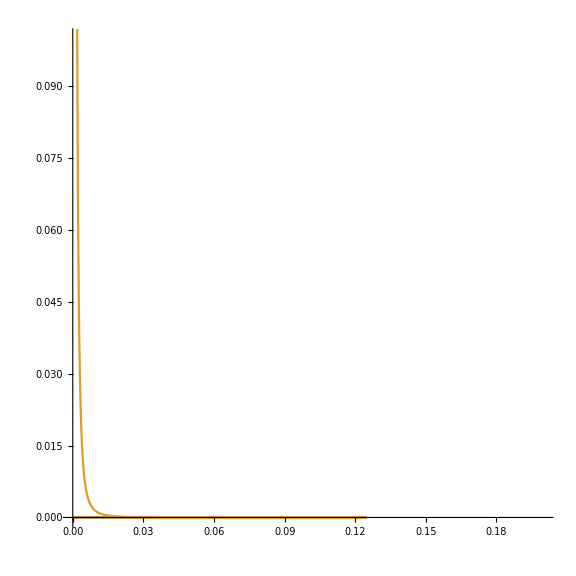

```mathematica
ParametricPlot[{{DangWxl[η], shear[η]},{DangWxl[η],expansion[η]}},{η,ηin,ETA0},ImageSize->Large,PlotRange->{{0,0.2},{0,0.1}}(*{{DangWxl[ETA0], DangWxl[ηin]},{-1,1}}*),AspectRatio->1]
```

```mathematica
δx={0,0,-10^-6/8,-10^-6/8};
δXf[t_]=𝒲[t][[1,2]].δx;
```

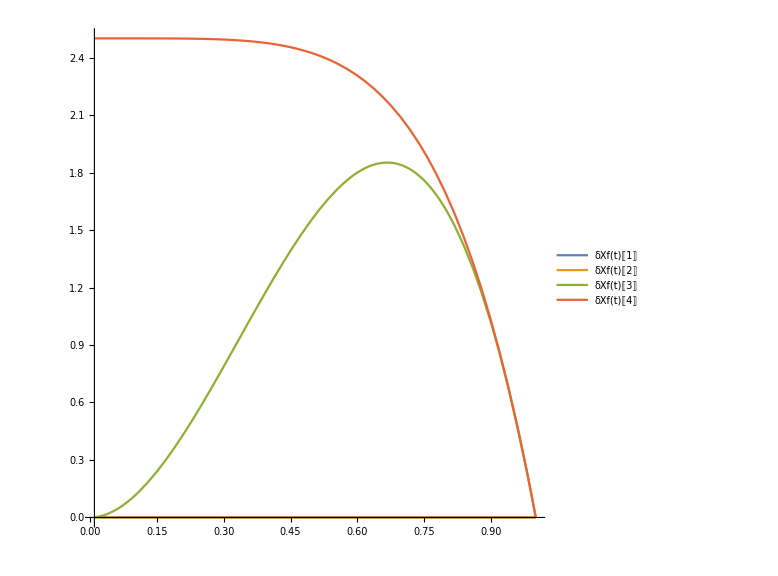

```mathematica
Plot[{δXf[t][[1]],δXf[t][[2]],δXf[t][[3]],δXf[t][[4]]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
δX0[t_]=(F0[t]/αα[t]).δXf[t]/.Join[param,totBG];
δX1[t_]=(F[t][[1]]-F0[t](ββ[t][[1]])/αα[t]).δXf[t]/.Join[param,totBG];
δX2[t_]=(F[t][[2]]-F0[t](ββ[t][[2]])/αα[t]).δXf[t]/.Join[param,totBG];
δX3[t_]=(F[t][[3]]-F0[t](ββ[t][[3]])/αα[t]).δXf[t]/.Join[param,totBG];
```

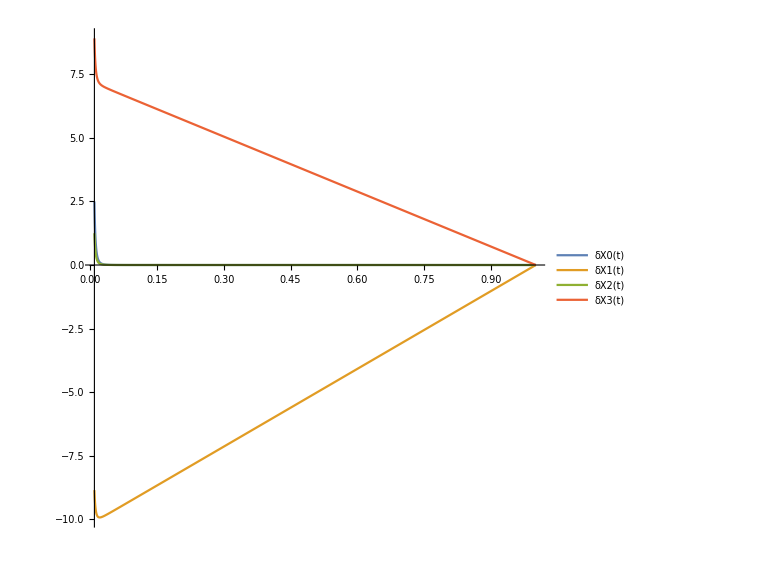

```mathematica
Plot[{δX0[t],δX1[t],δX2[t],δX3[t]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
Δx[t_]=-{δX0[t],δX1[t],δX2[t],δX3[t]}.ndown[t]/.Join[param,totBG];
ξ[t_]=({δX0[t],δX1[t],δX2[t],δX3[t]}-Δx[t]nup[t])/.Join[param,totBG];
```

```mathematica
Δx[ηin]
ξ[ηin]
```

0.000249999999975000122693

{0,-8.854145189105590659552,1.24999999987500061346,8.912476534011198821003}

```mathematica
δXc[t_]={ξ[t][[2]],ξ[t][[3]],ξ[t][[4]]};
trajectory[t_]=Evaluate[{x[t],y[t],z[t]}/.totBG];
Show[ParametricPlot3D[trajectory[η],{η,ηin,ETA0},PlotRange->{{-1,1},{-1,1},{-1,1}}](*/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]]*) ,Table[Graphics3D[{(*{Opacity[η/300+0.28],Black,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(Pu[η]/.totBG))}]},{Opacity[η/300+0.28],Green,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P1[η]/.totBG))}]},{Opacity[η/300+0.28],Blue,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P2[η]/.totBG))}]},{*)(*Opacity[η/300+0.28],*)Red,Arrowheads[0.01],Arrow[{trajectory[η],(trajectory[η]+1/10(δXc[η]/.totBG))}]}],{η,ηin,ETA0,(ETA0-ηin)/30}] , ImageSize->700,AxesLabel->{Style["x/(M̄)",Large],Style["y/(M̄)",Large],Style["z/(M̄)",Large]},AxesStyle->Directive[Black,12],Boxed->False,ViewPoint->{0,100,10}]
```

-Graphics3D-

{{{-((2.7237860069707152981421633620495074316144608192309597248700583241 (3.4641016151377545870548926830117447338856105076207612561116139589+0. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) JacobiDN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] JacobiSN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])/((-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.73205080756887729352744634150587236694280525381038062805580697945193+2.7320508075688772935274463415058723669428052538103806280558069794519 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]))),0,0,0},{0,Indeterminate,0,0},{0,0,-((2.7237860069707152981421633620495074316144608192309597248700583241 (3.4641016151377545870548926830117447338856105076207612561116139589+0. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) JacobiDN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] JacobiSN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])/((-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.73205080756887729352744634150587236694280525381038062805580697945193+2.7320508075688772935274463415058723669428052538103806280558069794519 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]))),0},{0,0,0,-((2.7237860069707152981421633620495074316144608192309597248700583241 (3.4641016151377545870548926830117447338856105076207612561116139589+0. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) JacobiDN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] JacobiSN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])/((-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.73205080756887729352744634150587236694280525381038062805580697945193+2.7320508075688772935274463415058723669428052538103806280558069794519 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])))}},{{0,(0.1547005383792515290182975610039149112952035025402537520372 JacobiDN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] JacobiSN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] ((0.+0. ⅈ) z^2 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.23287442231493+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.065143806481186+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^2 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.280835906085638+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^3 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.383903700136203+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^4 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-3.2688628827488073+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^5 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.211654059590725+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^6 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.211654059590725+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^7 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-3.2688628827488073+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^8 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.383903700136203+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^9 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.280835906079821+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^10 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.065143806476822+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^11 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.232874422311371+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^12 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0.+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^13 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2))/((-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^2 (1.+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.732050807568877293527446341505872366942805253810380628055807+2.73205080756887729352744634150587236694280525381038062805581 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^7 (0.071796769724490825890214633976510532228778984758477487776772+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^2) (((1.534671372856151603129538167133997507112075941+0. ⅈ)+(0.7320508075688772935274463415058723669428052538+0. ⅈ) y^2 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]+(0.7320508075688772935274463415058723669428052538+0. ⅈ) z^2 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]+(0.1821319774690423795896326343777034322594397092+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] √(((1.+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.07179676972449082589021463397651053222877898475847748777677208+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^2))/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] ((5.727471536420638182418394645602449996691046204+0. ⅈ)+((2.732050807568877293527446341505872366942805254+0. ⅈ) y^2+(2.732050807568877293527446341505872366942805254+0. ⅈ) z^2) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]-(0.1821319774690423795896326343777034322594397092+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] √(((1.+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.07179676972449082589021463397651053222877898475847748777677208+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^2))/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])))^2),0,0},{(0.1547005383792515290182975610039149112952035025402537520372 JacobiDN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] JacobiSN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] ((0.+0. ⅈ) z^2 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.23287442231493+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.065143806481186+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^2 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.280835906085638+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^3 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.383903700136203+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^4 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-3.2688628827488073+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^5 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.211654059590725+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^6 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.211654059590725+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^7 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-3.2688628827488073+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^8 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.383903700136203+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^9 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.280835906079821+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^10 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.065143806476822+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^11 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0``-4.232874422311371+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^12 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2+(0.+0. ⅈ) z^2 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^13 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]^2))/((-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^2 (1.+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.732050807568877293527446341505872366942805253810380628055807+2.73205080756887729352744634150587236694280525381038062805581 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^7 (0.071796769724490825890214633976510532228778984758477487776772+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^2) (((1.534671372856151603129538167133997507112075941+0. ⅈ)+(0.7320508075688772935274463415058723669428052538+0. ⅈ) y^2 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]+(0.7320508075688772935274463415058723669428052538+0. ⅈ) z^2 Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]+(0.1821319774690423795896326343777034322594397092+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] √(((1.+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.07179676972449082589021463397651053222877898475847748777677208+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^2))/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] ((5.727471536420638182418394645602449996691046204+0. ⅈ)+((2.732050807568877293527446341505872366942805254+0. ⅈ) y^2+(2.732050807568877293527446341505872366942805254+0. ⅈ) z^2) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]-(0.1821319774690423795896326343777034322594397092+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] √(((1.+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.07179676972449082589021463397651053222877898475847748777677208+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]^2))/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])))^2),(1. Cos[181.146430634095731182423482097145018267504243021850751551455323863724 x] ((86.40833026494401984488926495371099585003804629801198839436411+0. ⅈ) (y^2+z^2)-((5.9070614247140407730361653519966889875720213296565574974502+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) √(1-(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3))/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])))/(1+(0.4770081859326466737761614253961372233354583453352819296713384+0. ⅈ) (y^2+z^2) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]-((0.032609317247028340055733459862424025412196742850998552332814+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) √(1-(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])),((0.9540163718652933475523228507922744466709166906705638593426768+0. ⅈ) y Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(1+(0.4770081859326466737761614253961372233354583453352819296713384+0. ⅈ) (y^2+z^2) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]-((0.032609317247028340055733459862424025412196742850998552332814+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) √(1-(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])),((0.9540163718652933475523228507922744466709166906705638593426768+0. ⅈ) z Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(1+(0.4770081859326466737761614253961372233354583453352819296713384+0. ⅈ) (y^2+z^2) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]-((0.032609317247028340055733459862424025412196742850998552332814+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) √(1-(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]))},{0,((0.9540163718652933475523228507922744466709166906705638593426768+0. ⅈ) y Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(1+(0.4770081859326466737761614253961372233354583453352819296713384+0. ⅈ) (y^2+z^2) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]-((0.032609317247028340055733459862424025412196742850998552332814+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) √(1-(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])),0,0},{0,((0.9540163718652933475523228507922744466709166906705638593426768+0. ⅈ) z Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(1+(0.4770081859326466737761614253961372233354583453352819296713384+0. ⅈ) (y^2+z^2) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]-((0.032609317247028340055733459862424025412196742850998552332814+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) √(1-(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])),0,0}},{{0,0,-((2.7237860069707152981421633620495074316144608192309597248700583241 (3.4641016151377545870548926830117447338856105076207612561116139589+0. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) JacobiDN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] JacobiSN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])/((-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.73205080756887729352744634150587236694280525381038062805580697945193+2.7320508075688772935274463415058723669428052538103806280558069794519 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]))),0},{0,(-0.9540163718652933475523228507922744466709166906705638593426768+0. ⅈ) y Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x] (1+(0.4770081859326466737761614253961372233354583453352819296713384+0. ⅈ) (y^2+z^2) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]-((0.032609317247028340055733459862424025412196742850998552332814+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) √(1-(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])),0,0},{-((2.7237860069707152981421633620495074316144608192309597248700583241 (3.4641016151377545870548926830117447338856105076207612561116139589+0. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) JacobiDN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] JacobiSN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])/((-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.73205080756887729352744634150587236694280525381038062805580697945193+2.7320508075688772935274463415058723669428052538103806280558069794519 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]))),0,0,0},{0,0,0,0}},{{0,0,0,-((2.7237860069707152981421633620495074316144608192309597248700583241 (3.4641016151377545870548926830117447338856105076207612561116139589+0. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) JacobiDN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] JacobiSN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])/((-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.73205080756887729352744634150587236694280525381038062805580697945193+2.7320508075688772935274463415058723669428052538103806280558069794519 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])))},{0,(-0.9540163718652933475523228507922744466709166906705638593426768+0. ⅈ) z Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x] (1+(0.4770081859326466737761614253961372233354583453352819296713384+0. ⅈ) (y^2+z^2) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x]-((0.032609317247028340055733459862424025412196742850998552332814+0. ⅈ) Hypergeometric2F1[5/6,3/2,11/6,(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3] (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) √(1-(0.0490381056766579701455847561294042752071039403577854710418552345889 (-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3)/(0.2679491924311227064725536584941276330571947461896193719441930205481+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])^3) Sin[181.146430634095731182423482097145018267504243021850751551455323863724 x])/(0.26794919243112270647255365849412763305719474618961937194419302055+1. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])),0,0},{0,0,0,0},{-((2.7237860069707152981421633620495074316144608192309597248700583241 (3.4641016151377545870548926830117447338856105076207612561116139589+0. JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) JacobiDN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)] JacobiSN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)])/((-1.+JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]) (0.73205080756887729352744634150587236694280525381038062805580697945193+2.7320508075688772935274463415058723669428052538103806280558069794519 JacobiCN[2.72378600697071529814216336204950743161446081923095972487005832409607 s,1/4 (2+√3)]))),0,0,0}}}